# Genetic signatures of evolutionary rescue by a selective sweep

## Matthew M Osmond & Graham Coop

Center for Population Biology and Department of Evolution and Ecology, University of California - Davis

mmosmond@ucdavis.edu

## Prerequisites

### Directories

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
imagedir="../figures/";(*where to save plots*)
datadir="simulations/";(*where simulation data is*)
```

### Functions (derived in Methods below, and in manuscript)

#### Recursions

```mathematica
wbar=(1-d) (1-q[t])^2+2 (1-d) (1+h s) (1-q[t]) q[t]+(1-d) (1+s) q[t]^2;
qnew=(q[t] (-1-h s+(-1+h) s q[t]))/(-1-2 h s q[t]+(-1+2 h) s q[t]^2);
qtadditive={q[t]->(ⅇ^((s t)/2) q0)/(1+(-1+ⅇ^((s t)/2)) q0)};
ntadditive={n[t]->ⅇ^(-d t) N0 (1+(-1+ⅇ^((s t)/2)) q0)^(2-2 d)};
ntadditiveClonal={{n[t]->ⅇ^(-d t) N0 (1+(-1+ⅇ^((s t)/2)) q0)^(1-d)}};
```

#### Probability of establishment

```mathematica
pest=1-Exp[-2(w-1)/v];
```

#### Rescue from standing genetic variance

```mathematica
PSGV=1-(1-ρ)^κ;
q0rescueSGV=κ/(2N0)1/PSGV;
```

#### Rescue from de novo mutation

```mathematica
PDNM=1-ⅇ^(-(2 N0 ρ u)/d);
q0rescueDNM=((-c)^(-ϵ/d) (-Gamma[(d+ϵ)/d]+Gamma[(d+ϵ)/d,-c]))/(2 (-1+ⅇ^c) N0 ρ)/.c->u 2N0 ρ/d;
q0sweepDNM=1/(2N0 ρ);
```

#### Rescue from migration

```mathematica
PMIG=1-N0^(-(m ρ)/d);
q0rescueMIG=1/(2N0)1/ρ(m ρ  (1-N0^(-(ϵ+m ρ)/d)))/((ϵ+ m ρ) (1-N0^((-m ρ)/d)));
q0sweepMIG=1/(2N0 ρ);
```

#### Structured coalescent

```mathematica
pcoal[k_,τ_]:=Binomial[k,2] 1/(2ne[τ]x[τ])
preco[k_,τ_]:=k(2n[τ]r(1-x[τ]))/(2n[τ])
pmut[k_,τ_]:=k (2n[τ]u(1-x[τ]))/(2n[τ]x[τ])
pmig[k_,τ_]:=k m/(2n[τ]x[τ])
coalrate[n_,p_,τ_,l_,NeN_]:=(l(l-1))/(4n[[τ]] NeN p[[τ]])
coalEmp[n_,p_,l_,NeN_]:=Table[coalrate[n,p,τ,l,NeN],{τ,Length[p]}];(*prob of coal in gen τ*)

recrate[p_,τ_,l_,r_]:=l r(1-p[[τ]])
recEmp[p_,l_,r_]:=Table[recrate[p,τ,l,r],{τ,Length[p]}];(*prob of rec in gen τ*)

mutrate[p_,τ_,l_,u_]:=(l u(1-p[[τ]]))/p[[τ]]
mutEmp[p_,l_,u_]:=Table[mutrate[p,τ,l,u],{τ,Length[p]}];(*prob of mut in gen τ*)

migrate[l_,m_,n_,τ_,p_]:=(l m)/(2n[[τ]]p[[τ]])
migEmp[n_,p_,l_,m_]:=Table[migrate[l,m,n,τ,p],{τ,Length[p]}];(*prob of mig in gen τ*)
```

#### Backward-time dynamics

```mathematica
tfixadditive=(2 Log[((-1+q0) qf)/(q0 (-1+qf))])/s;
qtadditiveback[τ_]:=qf/(ⅇ^((s τ)/2) (1-qf)+qf)
ntadditiveback[τ_]:=ⅇ^(d τ) N0 (((1-q0) qf)/(q0 (1-qf)))^(-(2 d)/s) (1-q0+(ⅇ^(-(s τ)/2) (1-q0) qf)/(1-qf))^(2-2 d)
```

#### Probability of no events

```mathematica
cbackapprox[k_,τ_]:=1/(4 N0 NeN (-1+q0)^2 qf^3)(-1+k) k (-1+qf)^2 (((-1+q0) qf)/(q0 (-1+qf)))^((2 d)/s) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf^2)^(-2 d) (1/(d-s+d s)qf (((-1+q0) (-ⅇ^((s τ)/2) (-1+qf)+qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(-1+qf)/qf]-1/(d-s+d s)ⅇ^((-d+s) τ) qf (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]-1/(-3 s+2 d (1+s))2 ⅇ^(-d τ) (-1+qf) (ⅇ^(d τ) (((-1+q0) (-ⅇ^((s τ)/2) (-1+qf)+qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(-1+qf)/qf]-ⅇ^((3 s τ)/2) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]))
rbackapprox[k_,τ_]:=(2 k r (-ⅈ π+Log[ⅇ^((s τ)/2) (-1+qf)-qf]))/s
mutbackapprox[k_,τ_]:=-(2 (-1+ⅇ^((s τ)/2)) k (-1+qf) u)/(qf s)
migbackapprox[k_,τ_]:=1/(2 N0 NeN (-1+q0)^2)k m (-1+qf)^2 (1/qf)^(3-2 d) (((-1+q0) qf)/(q0 (-1+qf)))^((2 d)/s) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(-2 d) (1/(d-s+d s)((-1+q0)/(-1+qf))^(2 d) qf ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(-1+qf)/qf]-1/(d-s+d s)ⅇ^((-d+s) τ) (1/qf)^(-1+2 d) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/(-1+qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]-1/(-3 s+2 d (1+s))2 ⅇ^(-d τ) (-1+qf) (ⅇ^(d τ) ((-1+q0)/(-1+qf))^(2 d) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(-1+qf)/qf]-ⅇ^((3 s τ)/2) (1/qf)^(2 d) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/(-1+qf))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]))
cclassicbackapprox[k_,τ_]:=((-1+k) k (-(2 (-1+ⅇ^((s τ)/2)) (-1+qf))/s+qf τ))/(4 N0 NeN qf)
migclassicbackapprox[k_,τ_]:=(k m (-(2 (-1+ⅇ^((s τ)/2)) (-1+qf))/s+qf τ))/(2 N0 NeN qf)
cbottlebackapprox[k_,τ_]:=-1/(4 N0 NeN (-1+q0)^2 (d-s+d s))(-1+k) k (-1+qf)^2 (1/qf)^(2-2 d) (((-1+q0) qf)/(q0 (-1+qf)))^((2 d)/s) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(-2 d) (-((-1+q0)/(-1+qf))^(2 d) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(-1+qf)/qf]+ⅇ^((-d+s) τ) (1/qf)^(2 d) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/(-1+qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf])
pcoalbottle[k_,T_]:=1-Exp[-cbottlebackapprox[k,T]]

nothingyetEmp[c_,r_,m_,mig_,i_,τ_]:=Exp[-Accumulate[c[[i]]+r[[i]]+m[[i]]+mig[[i]]][[τ]]];
```

#### Haldane’s mapping function

```mathematica
haldane[r_]:=50*Log[1/(1-2Abs[r])]Sign[r]
```

### Plots

#### Style

```mathematica
defaultcolors=ColorData[1,"ColorList"];(*colors*)
labelstyle=Directive[FontSize->12,FontFamily->"Helvetica"];(*font for axis labels*)
letterstyle=Directive[FontSize->14,FontFamily->"Helvetica"];(*font for panel letters*)
letterposition={0.05,0.925};(*position of panel letters*)
padding={{60,10},{40,10}};(*padding around figures*)
Hpadding={{70,10},{40,10}};(*special case of padding for diversity plots*)
ylabelposition={-0.15,0.5};(*position of y-axis labels*)
Needs["ErrorBarPlots`"];(*for plotting error bars*)
```

#### Get backward-time simulation dynamics

```mathematica
getSimDynamics[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,maxt_,avg_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[0<uval,NumberForm[uval,{6,5}],0],If[0<mval<1,NumberForm[mval,{2,1}],mval]];(*folder where data is*)
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];(*data for each rep*)
allp=Table[data[i][[2;;,3]],{i,nreps}];(*allele frequencies, p*)
alln=Table[data[i][[2;;,2]],{i,nreps}];(*population sizes, n*)
allpcut=Table[allp[[i]][[1;;Module[{n=1},While[allp[[i]][[n]]<1,n++];n-1]]],{i,nreps}];(*consider fixed when p=1*)
allncut=Table[alln[[i]][[1;;Length[allpcut[[i]]]]],{i,nreps}];(*cut n when fixed*)
allpreversed=Reverse[allpcut,2];(*reverse p*)
allnreversed=Reverse[allncut,2];(*reverse n*)
allppadded=PadRight[allpreversed];(*pad p with zeros for taking the mean/median*)
allnpadded=PadRight[allnreversed-Nval]+Nval;(*pad n with N0 for taking the mean/median*)
maxT=Min[maxt,Length[allppadded[[1]]]];(*consider times up to min of plotting range, maxt, or max fixation time*)
listp=Table[Transpose[Join[{Table[-i,{i,maxT}]},{allppadded[[j,1;;maxT]]}]],{j,nreps}];(*add times to p for plotting*)
listn=Table[Transpose[Join[{Table[-i,{i,maxT}]},{allnpadded[[j,1;;maxT]]}]],{j,nreps}];(*add times to n for plotting*)
listpmean=avg[listp];(*take mean/median*)
listnmean=avg[listn];(*take mean/median*)
fixtimes=Table[Module[{n=1},While[allpreversed[[i]][[n]]>1/(2*Nval),n++]//Quiet;n-1],{i,nreps}];(*fixation times: time between p=1/2N0 and p=1*)
{listp,listn,listpmean,listnmean,fixtimes}(*return individual and mean/median dynamics and fixation times*)
)
```

```mathematica
getSimDynamicsClonal[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,maxt_,avg_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``_clonal",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[0<uval,NumberForm[uval,{6,5}],0],If[0<mval<1,NumberForm[mval,{3,2}],mval]];(*folder where data is*)
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];(*data for each rep*)
allp=Table[2*data[i][[2;;,3]],{i,nreps}];(*genotype frequencies, p*)
alln=Table[data[i][[2;;,2]],{i,nreps}];(*population sizes, n*)
allpcut=Table[allp[[i]][[1;;Module[{n=1},While[allp[[i]][[n]]<1,n++];n-1]]],{i,nreps}];(*consider fixed when p=1*)
allncut=Table[alln[[i]][[1;;Length[allpcut[[i]]]]],{i,nreps}];(*cut n when fixed*)
allpreversed=Reverse[allpcut,2];(*reverse p*)
allnreversed=Reverse[allncut,2];(*reverse n*)
allppadded=PadRight[allpreversed];(*pad p with zeros for taking the mean/median*)
allnpadded=PadRight[allnreversed-Nval]+Nval;(*pad n with N0 for taking the mean/median*)
maxT=Min[maxt,Length[allppadded[[1]]]];(*consider times up to min of plotting range, maxt, or max fixation time*)
listp=Table[Transpose[Join[{Table[-i,{i,maxT}]},{allppadded[[j,1;;maxT]]}]],{j,nreps}];(*add times to p for plotting*)
listn=Table[Transpose[Join[{Table[-i,{i,maxT}]},{allnpadded[[j,1;;maxT]]}]],{j,nreps}];(*add times to n for plotting*)
listpmean=avg[listp];(*take mean/median*)
listnmean=avg[listn];(*take mean/median*)
fixtimes=Table[Module[{n=1},While[allpreversed[[i]][[n]]>1/Nval,n++]//Quiet;n-1],{i,nreps}];(*fixation times: time between p=1/N0 and p=1*)
{listp,listn,listpmean,listnmean,fixtimes}(*return individual and mean/median dynamics and fixation times*)
)
```

#### Predict backward-time theoretical dynamics

```mathematica
backwardsTheory[dval_,kval_,uval_,Nval_]:=
(
q0=
(*effective initial frequency*)
If[dval>0,
If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]],
If[kval>0,q0rescueSGV ,If[uval>0,q0sweepDNM,q0sweepMIG]]
]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-dval);
(*effective final frequency*)
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-dval)(1+s)/.W->(1-dval)(1+s h);
(*backwards time allele frequency dynamics*)
xsol=x[t_]->qtadditiveback[t];
(*backwards time population size dynamics*)
If[dval>0,
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0],
nsol=n[t_]->N0
];
(*fixation time*)
tmax=Re[tfixadditive]/.N0->Nval/.params;
(*add times to p for plotting*)
listp=Table[{-t,x[tmax-t]/.xsol/.N0->Nval/.params},{t,0,tmax}];
(*add times to n for plotting*)
listn=Table[{-t,n[tmax-t]/.nsol/.N0->Nval/.params},{t,0,tmax}];
Clear[q0,qf];
{listp,listn,tmax}
)
```

```mathematica
backwardsTheoryClonal[dval_,kval_,uval_,Nval_]:=
(
q0=2*
(*effective initial frequency*)
If[dval>0,
If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]],
If[kval>0,q0rescueSGV ,If[uval>0,q0sweepDNM,q0sweepMIG]]
]/.ϵ->w-1/.ρ->pest/.v->(B-w) w/.w->(1+h s)(1-dval);
(*effective final frequency*)
qf=1-1/(N0 ρ2)/.ρ2->pest/.v->((B-W) W)/Wbar^2/.w->ϵ+1/.ϵ->1-W/Wbar/.W->(1-dval)/.Wbar->(1+s h)(1-dval);
(*backwards time allele frequency dynamics*)
xsol=x[t_]->qtadditiveback[t];
(*backwards time population size dynamics*)
If[dval>0,
nsol=n[t_]->Min[Re[ntadditivebackClonal[t]],N0],
nsol=n[t_]->N0
];
(*fixation time*)
tmax=Re[tfixadditive]/.N0->Nval/.params;
(*add times to p for plotting*)
listp=Table[{-t,x[tmax-t]/.xsol/.N0->Nval/.params},{t,0,tmax}];
(*add times to n for plotting*)
listn=Table[{-t,n[tmax-t]/.nsol/.N0->Nval/.params},{t,0,tmax}];
Clear[q0,qf];
{listp,listn,tmax}
)
```

#### Plot backwards-time dynamics, rescue vs constant population size

Plot dynamics backwards in time

```mathematica
plotDynamicsBackwards[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,maxt_,letter_,save_,nreps_,avg_]:=
(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,B->2};

(*tick marks for x-axis*)
ticks={Table[{-x,x},{x,0,maxt,50}],Automatic,None,None};

(*rescue: simulations*)
{pRescue,nRescue,pMeanRescue,nMeanRescue,fixTimesRescue}=getSimDynamics[Nval,dval,sval,hval,kval,uval,mval,nreps,maxt,avg];

(*constant: simulations*)
{pSweep,nSweep,pMeanSweep,nMeanSweep,fixTimesSweep}=getSimDynamics[Nval,0,sval,hval,kval,uval,mval,nreps,maxt,avg];

(*rescue: theory*)
{pTheoryRescue,nTheoryRescue,fixTimeTheoryRescue}=backwardsTheory[dval,kval,uval,Nval];

(*constant theory*)
{pTheorySweep,nTheorySweep,fixTimeTheorySweep}=backwardsTheory[0,kval,uval,Nval];

(*frame style and plotting fixation times*)
starheight=-0.025;
arrowheight=0.05;
topstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="C",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="D",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
}
];
bottomstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic}
},
letter=="C",
{
FrameTicksStyle->{Automatic,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
},
FrameLabel->{"Generations before fixation"}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Generations before fixation"}
}
];

(*plotting allele frequency dynamics*)
pdynamics=Show[
ListPlot[
pSweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01}}
],
ListPlot[
pRescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01}}
],
ListPlot[
{pTheorySweep,pTheoryRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[2]],AbsoluteThickness[3]],Directive[defaultcolors[[1]],AbsoluteThickness[3]]},
PlotRange->{{-maxt,0},{0,1.01}}
],
(*ListPlot[
{pMeanSweep,pMeanRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.8]],Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.8]]},
PlotRange->{{-maxt,0},{0,1.01}}
],*)
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,1.01}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
topstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["pdynamics_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],pdynamics];
];

(*plotting population size dynamics*)
ndynamics=Show[
ListPlot[
nSweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
ListPlot[
nRescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
ListPlot[
{nTheorySweep,nTheoryRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[2]],AbsoluteThickness[3]],Directive[defaultcolors[[1]],AbsoluteThickness[3]]},
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
(*ListPlot[
{nMeanSweep,nMeanRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.8]],Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.8]]},
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],*)
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,1.01*Nval}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
bottomstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["ndynamics_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],ndynamics];
];

GraphicsColumn[{pdynamics,ndynamics},ImageSize->400,Spacings->0]
)
```

#### Plot backwards-time dynamics, clonal

Plot dynamics backwards in time, with clonal model

```mathematica
plotDynamicsBackwardsClonal[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,maxt_,letter_,save_,nreps_,avg_]:=
(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,B->2};

(*tick marks for x-axis*)
ticks={Table[{-x,x},{x,0,maxt,50}],Automatic,None,None};

(*simulations*)
{pSweep,nSweep,pMeanSweep,nMeanSweep,fixTimesSweep}=getSimDynamicsClonal[Nval,dval,sval,hval,kval,uval,mval,nreps,maxt,avg];

(*theory*)
{pTheorySweep,nTheorySweep,fixTimeTheorySweep}=backwardsTheoryClonal[dval,kval,uval,Nval];

(*frame style and plotting fixation times*)
starheight=-0.025;
arrowheight=0.05;
topstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="C",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="D",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Text[Style[★,16,defaultcolors[[2]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[2]]],{-Mean[fixTimesSweep],arrowheight}]
}
}
];
bottomstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic}
},
letter=="C",
{
FrameTicksStyle->{Automatic,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
},
FrameLabel->{"Generations before fixation"}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Generations before fixation"}
}
];

(*plotting allele frequency dynamics*)
pdynamics=Show[
ListPlot[
pSweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01}}
],
ListPlot[
pTheorySweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[3]],
PlotRange->{{-maxt,0},{0,1.01}}
],
ListPlot[
pMeanSweep,
Joined->True,
PlotStyle->Directive[Red,AbsoluteThickness[2],Opacity[0.8],Dashed],
PlotRange->{{-maxt,0},{0,1.01}}
],
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,1.01}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
topstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["pdynamics_rescue_s``_k``_u``_m``_clonal.pdf",sval,kval,uval,mval]],pdynamics];
];

(*plotting population size dynamics*)
ndynamics=Show[
ListPlot[
nSweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
ListPlot[
nTheorySweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[3]],
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
ListPlot[
nMeanSweep,
Joined->True,
PlotStyle->Directive[Red,AbsoluteThickness[2],Opacity[0.8],Dashed],
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,1.01*Nval}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
bottomstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["ndynamics_rescue_s``_k``_u``_m``_clonal.pdf",sval,kval,uval,mval]],ndynamics];
];

GraphicsColumn[{pdynamics,ndynamics},ImageSize->400,Spacings->0]
)
```

#### Get coalescent estimates from simulations

```mathematica
getSimCoalescent[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_,maxt_,lval_,rval_]:=
(
(*get time reversed p and n dynamics, as in getSimDynamics[]*)
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[0<uval,NumberForm[uval,{6,5}],0],If[0<mval<1,NumberForm[mval,{2,1}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];
allp=Table[data[i][[2;;,3]],{i,nreps}];
alln=Table[data[i][[2;;,2]],{i,nreps}];
allpcut=Table[
allp[[i]][[1;;Module[{n=1},While[allp[[i]][[n]]<1,n++];n-1]]],
{i,nreps}];
allncut=Table[alln[[i]][[1;;Length[allpcut[[i]]]]],{i,nreps}];
allpreversed=Reverse[allpcut,2];
allnreversed=Reverse[allncut,2];
allpreversedcut=Table[
allpreversed[[i]][[1;;Min[Module[{n=1},While[allpreversed[[i]][[n]]>1/(2Nval),n++]//Quiet;n-1],maxt]]],
{i,nreps}];
allnreversedcut=Table[allnreversed[[i]][[1;;Length[allpreversedcut[[i]]]]],{i,nreps}];

(*calculate coalescent rates*)
coalEmpTabs=Table[coalEmp[allnreversedcut[[i]],allpreversedcut[[i]],lval,4/7],{i,nreps}];(*instantaneous coal rates*)
recEmpTabs=Table[recEmp[allpreversedcut[[i]],lval,rval],{i,nreps}];(*instantaneous rec rates*)
mutEmpTabs=Table[mutEmp[allpreversedcut[[i]],lval,uval],{i,nreps}];(*instantaneous mut rates*)
migEmpTabs=Table[migEmp[allnreversedcut[[i]],allpreversedcut[[i]],lval,mval],{i,nreps}];(*instantaneous mig rates*)

nothingyetTabs=Table[Table[nothingyetEmp[coalEmpTabs,recEmpTabs, mutEmpTabs,migEmpTabs,i,τ],{τ,Length[coalEmpTabs[[i]]]}],{i,nreps}];(*prob no events by gen τ*)

coalEmpTabs=Table[Table[coalEmpTabs[[i,τ]]nothingyetTabs[[i,τ]],{τ,Length[coalEmpTabs[[i]]]}],{i,nreps}];(*prob coal in gen τ*)
recEmpTabs=Table[Table[recEmpTabs[[i,τ]]nothingyetTabs[[i,τ]],{τ,Length[recEmpTabs[[i]]]}],{i,nreps}];(*prob rec in gen τ*)
mutEmpTabs=Table[Table[mutEmpTabs[[i,τ]]nothingyetTabs[[i,τ]],{τ,Length[mutEmpTabs[[i]]]}],{i,nreps}];(*prob mut in gen τ*)
migEmpTabs=Table[Table[migEmpTabs[[i,τ]]nothingyetTabs[[i,τ]],{τ,Length[migEmpTabs[[i]]]}],{i,nreps}];(*prob mig in gen τ*)

coalEmpTabs=Table[{-τ,Mean[Select[PadRight[coalEmpTabs][[All,τ]],#>0&]]},{τ,Length[PadRight[coalEmpTabs][[1]]]}];(*mean prob coal in gen τ, with time added for plotting*)
recEmpTabs=Table[{-τ,Mean[Select[PadRight[recEmpTabs][[All,τ]],#>0&]]},{τ,Length[PadRight[recEmpTabs][[1]]]}];(*mean prob rec in gen τ, with time added for plotting*)
mutEmpTabs=Table[{-τ,Mean[Select[PadRight[mutEmpTabs][[All,τ]],#>0&]]},{τ,Length[PadRight[mutEmpTabs][[1]]]}];(*mean prob mut in gen τ, with time added for plotting*)
migEmpTabs=Table[{-τ,Mean[Select[PadRight[migEmpTabs][[All,τ]],#>0&]]},{τ,Length[PadRight[migEmpTabs][[1]]]}];(*mean prob mig in gen τ, with time added for plotting*)

{coalEmpTabs,recEmpTabs,mutEmpTabs,migEmpTabs}(*return prob of events for plotting*)
)
```

#### Plot the coalescent, rescue vs constant population size

```mathematica
plotCoalescentSims[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,lval_,rval_,maxt_,ymax_,letter_,save_,nreps_]:=
(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->lval,r->rval,NeN->4/7,B->2};

(*x-axis tick marks*)
ticks={Table[{-x,x},{x,0,maxt,50}],Automatic,None,None};

(*frame style*)
bottomstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability",labelstyle],Scaled@ylabelposition],π/2]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{Text[Style[letter,letterstyle],Scaled@letterposition]}
},
letter=="C",
{
FrameTicksStyle->{Automatic,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability",labelstyle],Scaled@ylabelposition],π/2]
},
FrameLabel->{"Generations before fixation"}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
Epilog->{Text[Style[letter,letterstyle],Scaled@letterposition]},
FrameLabel->{"Generations before fixation"}
}
];

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d);
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h);
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0];
xsol=x[t_]->qtadditiveback[t];
tmax=Re[tfixadditive/.params];tmaxrescue=tmax;
nothingyet[l_,τ_]:=
Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]-migbackapprox[l,τ]];
rescuecoal=Table[{-τ,Re[pcoal[l,τ]nothingyet[l,τ]/.ne[t_]->n[t]NeN/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuerec=Table[{-τ,Re[preco[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuemut=Table[{-τ,Re[pmut[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuemig=Table[{-τ,Re[pmig[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];

(*constant theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0;
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.d->0;
nsol=n[t_]->N0;
xsol=x[t_]->qtadditiveback[t];
tmax=tfixadditive/.params;
nothingyetc[l_,τ_]:=
Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]-mutbackapprox[l,τ]];
sweepcoal=Table[{-τ,Re[pcoal[l,τ]nothingyetc[l,τ]/.ne[t_]->n[t] NeN/.xsol/.nsol/.params]},{τ,0,tmax}];
sweeprec=Table[{-τ,Re[preco[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
sweepmut=Table[{-τ,Re[pmut[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
sweepmig=Table[{-τ,Re[pmig[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];

(*rescue: simulations*)
{coalEmpRescue,recEmpRescue,mutEmpRescue,migEmpRescue}=getSimCoalescent[Nval,dval,sval,kval,uval,mval,nreps,maxt,lval,rval];

(*constant: simulations*)
{coalEmpSweep,recEmpSweep,mutEmpSweep,migEmpSweep}=getSimCoalescent[Nval,0,sval,kval,uval,mval,nreps,maxt,lval,rval];

coalescent=Show[
ListPlot[
{rescuecoal,sweepcoal},
Joined->True,
PlotRange->All,
PlotStyle->AbsoluteThickness[3],
Axes->False
],
ListPlot[
{rescuerec,sweeprec},
Joined->True,
PlotRange->All,
PlotStyle->Directive[AbsoluteThickness[3],Dashing[Large]]
],
ListPlot[
{rescuemut,sweepmut},
Joined->True,
PlotRange->All,
PlotStyle->If[uval>0,Directive[AbsoluteThickness[3],Dotted],Directive[AbsoluteThickness[0],White]]
],
ListPlot[
{rescuemig,sweepmig},
Joined->True,
PlotRange->All,
PlotStyle->If[mval>0,Directive[AbsoluteThickness[3],Dotted],Directive[AbsoluteThickness[0],White]]
],
ListPlot[
coalEmpSweep,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.5]],
Axes->False
],
ListPlot[
recEmpSweep,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.5],Dashed],
Axes->False
],
ListPlot[
mutEmpSweep,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.5],Dotted],
Axes->False
],
ListPlot[
migEmpSweep,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.5],Dotted],
Axes->False
],
ListPlot[
coalEmpRescue,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.5]],
Axes->False
],
ListPlot[
recEmpRescue,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.5],Dashed],
Axes->False
],
ListPlot[
mutEmpRescue,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.5],Dotted],
Axes->False
],
ListPlot[
migEmpRescue,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.5],Dotted],
Axes->False
],
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,ymax}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
bottomstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["coalescent_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],coalescent];
];

Clear[q0,qf];
GraphicsColumn[{coalescent},ImageSize->400,Spacings->0]
)
```

#### Get simulation diversity

```mathematica
getSimDiversity[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[uval>0,NumberForm[uval,{6,5}],0],mval];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allH=Table[data[i][[All,{1,2}]],{i,nreps}];(*pairwise diversity at a given physical distance for all reps*)
allH[[All,All,1]]=haldane[allH[[All,All,1]]];(*convert physical distance to cM*)
meanH=Mean/@Flatten[allH,{{2},{1}}];(*take mean across reps*)
{allH,meanH}(*return each rep and mean*)
)
```

#### Plot relative pairwise diversity, rescue vs constant population size

Plot pairwise nucleotide diversity divided by predicted background diversity

```mathematica
plotDiversityRelative[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,letter_,save_,nrs_]:=
(
(*parameters*)
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->2,U->6*10^-9,rbp->2*10^-8,B->2,NeN->4/7};
(*recombination distances to calculate theory at*)
rmin=0;rmax=0.2;rint=(2rmax)/nrs;
(*plotting ranges*)
xmin=-20;xmax=20;
ymax=2;

(*frame styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Relative mean pairwise diversity, π/π̄"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Relative mean pairwise diversity, π/π̄"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
{allHrescue,meanHrescue}=getSimDiversity[Nval,dval,sval,hval,kval,uval,mval,nreps];
backgroundH=Mean[Select[meanHrescue,Abs[#[[1]]]>5&][[All,2]]];(*mean diversity away from selected site*)
allHrescue[[All,All,2]]=allHrescue[[All,All,2]]/backgroundH;(*relativize individual replicates*)
meanHrescue[[All,2]]=meanHrescue[[All,2]]/backgroundH;(*relativize mean*)

(*constant: simulations*)
{allHsweep,meanHsweep}=getSimDiversity[Nval,0,sval,hval,kval,uval,mval,nreps];
backgroundH=Mean[Select[meanHsweep,Abs[#[[1]]]>5&][[All,2]]];(*mean diversity away from selected site*)
allHsweep[[All,All,2]]=allHsweep[[All,All,2]]/backgroundH;(*relativize individual replicates*)
meanHsweep[[All,2]]=meanHsweep[[All,2]]/backgroundH;(*relativize mean*)

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;(*effective initial frequency*)
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.params;(*effective final frequency*)
xsol=x[t_]->qtadditiveback[t];(*allele frequency dynamics backwards in time*)
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0];(*population size dynamics backwards in time*)
tmax=Re[tfixadditive/.params];(*fixation time*)
tab=Table[
{
haldane[r],(*cM*)
Sum[
Which[
kval>0,preco[l,τ]Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-migbackapprox[l,τ]]
]/.xsol/.nsol/.params,
{τ,0,tmax}],(*prob of getting off the selected background*)
If[kval>1,Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax/.params(*probability of no events*)
},
{r,rmin,rmax,rint}];
(*predict with theoretical θ:*)
tab1=Table[{tab[[i,1]],(tab[[i,2]]+tab[[i,3]]/(1-pcoalbottle[l,tmax]))/.params},{i,Length[tab]}];(*fraction of diversity remaining across all recombination distances*)
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works for plotting*)
rescue=Join[tab2,tab1];(*join negative and positive*)

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0/.params;
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.d->0/.params;
xsol=x[t_]->qtadditiveback[t];
nsol=n[t_]->N0;
tmax=Re[tfixadditive/.params];
tab1=Table[{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]]
]/.xsol/.nsol/.params,
{τ,0,tmax}];
Pnothing=If[kval>0,Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax;
Re[Poff+Pnothing/.params]
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];
sweep=Join[tab2,tab1];

(*plot*)
plot=Show[
ListPlot[
allHrescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],
Axes->False
],
ListPlot[
{sweep,rescue},
Joined->True,
PlotStyle->{
Directive[AbsoluteThickness[3],defaultcolors[[2]],Dashing[0]],
Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[0]]
},
Axes->False,
PlotRange->All
],
ListPlot[
{meanHrescue,meanHsweep},
Joined->True,
Axes->False,
PlotStyle->Directive[Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->{xticks,yticks,None,None},
style,
PlotRangePadding->None,
ImagePadding->Hpadding
];
If[save==1,
Export[imagedir<>ToString[StringForm["EH_rescue_s``_k``_u``_m``_relative.pdf",sval,kval,uval,mval]],plot];
];

Clear[q0,qf,allH,allHs];
Show[plot,ImageSize->400]
)
```

#### Plot absolute pairwise diversity, rescue vs constant population size

Plot pairwise nucleotide diversity

```mathematica
plotDiversity[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,letter_,save_,nrs_]:=
(
(*parameters*)
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->2,U->6*10^-9,rbp->2*10^-8,B->2,NeN->4/7};
(*recombination distances to calculate theory at*)
rmin=0;rmax=0.2;rint=(2rmax)/nrs;
(*plotting ranges*)
xmin=-20;xmax=20;
ymax=1.5*4N0 NeN U/.params;

(*frame styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Mean pairwise diversity, π"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Mean pairwise diversity, π"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
{allHrescue,meanHrescue}=getSimDiversity[Nval,dval,sval,hval,kval,uval,mval,nreps];

(*constant: simulations*)
{allHsweep,meanHsweep}=getSimDiversity[Nval,0,sval,hval,kval,uval,mval,nreps];

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;(*effective initial frequency*)
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.params;(*effective final frequency*)
xsol=x[t_]->qtadditiveback[t];(*allele frequency dynamics backwards in time*)
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0];(*population size dynamics backwards in time*)
tmax=Re[tfixadditive/.params];(*fixation time*)
tab=Table[
{
haldane[r],(*cM*)
Sum[
Which[
kval>0,preco[l,τ]Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-migbackapprox[l,τ]]
]/.xsol/.nsol/.params,
{τ,0,tmax}],(*prob of getting off the selected background*)
If[kval>1,Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax/.params(*probability of no events*)
},
{r,rmin,rmax,rint}];
(*predict with theoretical θ:*)
tab1=Table[{tab[[i,1]],(tab[[i,2]]*(1-pcoalbottle[l,tmax])+tab[[i,3]])4N0 NeN U/.params},{i,Length[tab]}];(*fraction of diversity remaining across all recombination distances*)
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works for plotting*)
rescueTheory=Join[tab2,tab1];(*join negative and positive*)
(*predict with observed θ:*)
backgroundHrescue=Mean[Select[meanHrescue,Abs[#[[1]]]>5&][[All,2]]];(*estimate of background diversity excluding sites within 5cM of selected site*)
tab1=Table[{tab[[i,1]],(tab[[i,2]]*backgroundHrescue+tab[[i,3]]*4N0 NeN U)/.params},{i,Length[tab]}];(*fraction of diversity remaining across all recombination distances*)
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works for plotting*)
rescueEmp=Join[tab2,tab1];

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0/.params;
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.d->0/.params;
xsol=x[t_]->qtadditiveback[t];
nsol=n[t_]->N0;
tmax=Re[tfixadditive/.params];
tab1=Table[{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]]
]/.xsol/.nsol/.params,
{τ,0,tmax}];
Pnothing=If[kval>1,Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax;
Re[ Poff*4N0 U NeN*Exp[-tmax/(2N0 NeN)]+Pnothing*4N0 U NeN/.params]
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];
sweep=Join[tab2,tab1];

(*plot*)
plot=Show[
ListPlot[
allHrescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],
Axes->False
],
ListPlot[
{sweep,rescueTheory},
Joined->True,
PlotStyle->{
Directive[AbsoluteThickness[3],defaultcolors[[2]],Dashing[0]],
Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[0]]
},
Axes->False,
PlotRange->All
],
ListPlot[
rescueEmp,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[Large]],
Axes->False,
PlotRange->All
],
ListPlot[
{meanHrescue,meanHsweep},
Joined->True,
Axes->False,
PlotStyle->Directive[Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->{xticks,yticks,None,None},
style,
PlotRangePadding->None,
ImagePadding->Hpadding
];
If[save==1,
Export[imagedir<>ToString[StringForm["EH_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],plot];
];

Clear[q0,qf,allH,allHs];
Show[plot,ImageSize->400]
)
```

#### Get simulation Tajima’s D

```mathematica
getSimD[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[uval>0,NumberForm[uval,{6,5}],0],mval];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allD=Table[data[i][[All,{1,3}]],{i,nreps}];
allD[[All,All,1]]=haldane[allD[[All,All,1]]];
meanD=Mean/@Flatten[allD,{{2},{1}}];
{allD,meanD}
)
```

#### Plot Tajima’s D, rescue vs constant population size

```mathematica
plotTajimasD[Nval_, dval_, sval_, hval_, kval_, uval_, mval_, nreps_, letter_, save_] :=
 (
  params = {N0 ->Nval, d ->dval, s -> sval, h -> hval, k -> kval, u -> uval, m -> mval};
  xmin = -20; xmax = 20;
  ymin = -4; ymax = 4;
  paramposition = {0.85, 0.1};
  
  ticks = {Table[{x, Abs[x]}, {x, xmin, xmax, 10}], Automatic, None, None};
  style = Which[
    letter == "A",
    {
     FrameLabel -> {, "Tajima's D"},
     FrameTicksStyle -> {FontColor -> White, Automatic, Automatic, Automatic},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     },
    letter == "B",
    {
     FrameTicksStyle -> {FontColor -> White, FontColor -> White, Automatic, Automatic},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     },
    letter == "C",
    {
     FrameLabel -> {"Distance from selected site (cM)", "Tajima's D"},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     },
    letter == "D",
    {
     FrameTicksStyle -> {Automatic, FontColor -> White, Automatic, Automatic},
     FrameLabel -> {"Distance from selected site (cM)",},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     }
    ];
  
  (*rescue: simulations*)
  {allDrescue,meanDrescue}=getSimD[Nval,dval,sval,kval,uval,mval,nreps];
  
  (*constant: simulations*)
  {allDsweep,meanDsweep}=getSimD[Nval,0,sval,kval,uval,mval,nreps];
  
  (*plot*)
  plot = Show[
    ListPlot[allDrescue, Joined -> True, PlotStyle -> Directive[defaultcolors[[1]], Thickness[0.001], Opacity[0.1]], Axes -> False],
    ListPlot[{meanDrescue, meanDsweep}, Joined -> True, Axes -> False, PlotStyle -> Directive[Thickness[0.005], Opacity[0.8]]
     ],
    PlotRange -> {{xmin, xmax}, {ymin, ymax}},
    Frame -> {True, True, False, False},
    FrameStyle -> labelstyle,
    FrameTicks -> ticks,
    PlotRangePadding -> None,
    style,
    ImagePadding -> Hpadding
    ];
If[save==1,
Export[imagedir <> ToString[StringForm["TajimasD_rescue_s``_k``_u``_m``.pdf", sval, kval, uval, mval]], plot]
];
  
  Show[plot, ImageSize -> 400]
  )
```

#### Plot backwards-time dynamics, rescue vs bottleneck

Plot dynamics backwards in time

```mathematica
plotDynamicsBackwardsBottleneck[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,maxt_,letter_,save_,nreps_,avg_,Nvalbottle_]:=
(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,B->2};

(*tick marks for x-axis*)
ticks={Table[{-x,x},{x,0,maxt,50}],Automatic,None,None};

(*rescue: simulations*)
{pRescue,nRescue,pMeanRescue,nMeanRescue,fixTimesRescue}=getSimDynamics[Nval,dval,sval,hval,kval,uval,mval,nreps,maxt,avg];

(*constant: simulations*)
{pSweep,nSweep,pMeanSweep,nMeanSweep,fixTimesSweep}=getSimDynamics[Nvalbottle,0,sval,hval,kval,uval,mval,nreps,maxt,avg];

(*rescue: theory*)
{pTheoryRescue,nTheoryRescue,fixTimeTheoryRescue}=backwardsTheory[dval,kval,uval,Nval];

(*constant theory*)
{pTheorySweep,nTheorySweep,fixTimeTheorySweep}=backwardsTheory[0,kval,uval,Nvalbottle];

(*frame style and plotting fixation times*)
starheight=-0.025;
arrowheight=0.05;
topstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[3]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[3]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[3]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[3]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="C",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[3]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[3]]],{-Mean[fixTimesSweep],arrowheight}]
}
},
letter=="D",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Text[Style[★,16,defaultcolors[[1]]],{-fixTimeTheoryRescue,starheight}],
Text[Style[★,16,defaultcolors[[3]]],{-fixTimeTheorySweep,starheight}],
Text[Style["↓",16,defaultcolors[[1]]],{-Mean[fixTimesRescue],arrowheight}],
Text[Style["↓",16,defaultcolors[[3]]],{-Mean[fixTimesSweep],arrowheight}]
}
}
];
bottomstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic}
},
letter=="C",
{
FrameTicksStyle->{Automatic,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
},
FrameLabel->{"Generations before fixation"}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Generations before fixation"}
}
];

(*plotting allele frequency dynamics*)
pdynamics=Show[
ListPlot[
pSweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[3]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01}}
],
ListPlot[
pRescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01}}
],
ListPlot[
{pTheorySweep,pTheoryRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[3]],AbsoluteThickness[3]],Directive[defaultcolors[[1]],AbsoluteThickness[3]]},
PlotRange->{{-maxt,0},{0,1.01}}
],
(*ListPlot[
{pMeanSweep,pMeanRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.8]],Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.8]]},
PlotRange->{{-maxt,0},{0,1.01}}
],*)
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,1.01}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
topstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["pdynamics_rescue_s``_k``_u``_m``_bottle.pdf",sval,kval,uval,mval]],pdynamics];
];

(*plotting population size dynamics*)
ndynamics=Show[
ListPlot[
nSweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[3]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
ListPlot[
nRescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[1],Opacity[0.1]],
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
ListPlot[
{nTheorySweep,nTheoryRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[3]],AbsoluteThickness[3]],Directive[defaultcolors[[1]],AbsoluteThickness[3]]},
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],
(*ListPlot[
{nMeanSweep,nMeanRescue},
Joined->True,
PlotStyle->{Directive[defaultcolors[[2]],AbsoluteThickness[2],Opacity[0.8]],Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.8]]},
PlotRange->{{-maxt,0},{0,1.01*Nval}}
],*)
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,1.01*Nval}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
bottomstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["ndynamics_rescue_s``_k``_u``_m``_bottle.pdf",sval,kval,uval,mval]],ndynamics];
];

GraphicsColumn[{pdynamics,ndynamics},ImageSize->400,Spacings->0]
)
```

#### Plot the coalescent, rescue vs bottleneck

```mathematica
plotCoalescentSimsBottleneck[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,lval_,rval_,maxt_,ymax_,letter_,save_,nreps_,Nvalbottle_]:=
(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->lval,r->rval,NeN->4/7,B->2};

(*x-axis tick marks*)
ticks={Table[{-x,x},{x,0,maxt,50}],Automatic,None,None};

(*frame style*)
bottomstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability",labelstyle],Scaled@ylabelposition],π/2]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{Text[Style[letter,letterstyle],Scaled@letterposition]}
},
letter=="C",
{
FrameTicksStyle->{Automatic,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability",labelstyle],Scaled@ylabelposition],π/2]
},
FrameLabel->{"Generations before fixation"}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
Epilog->{Text[Style[letter,letterstyle],Scaled@letterposition]},
FrameLabel->{"Generations before fixation"}
}
];

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d);
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h);
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0];
xsol=x[t_]->qtadditiveback[t];
tmax=Re[tfixadditive/.params];tmaxrescue=tmax;
nothingyet[l_,τ_]:=
Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]-migbackapprox[l,τ]];
rescuecoal=Table[{-τ,Re[pcoal[l,τ]nothingyet[l,τ]/.ne[t_]->n[t]NeN/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuerec=Table[{-τ,Re[preco[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuemut=Table[{-τ,Re[pmut[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuemig=Table[{-τ,Re[pmig[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];

(*constant theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0;
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.d->0;
nsol=n[t_]->N0;
xsol=x[t_]->qtadditiveback[t];
tmax=tfixadditive/.N0->Nvalbottle/.params;
nothingyetc[l_,τ_]:=
Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]-mutbackapprox[l,τ]];
sweepcoal=Table[{-τ,Re[pcoal[l,τ]nothingyetc[l,τ]/.ne[t_]->n[t] NeN/.xsol/.nsol/.N0->Nvalbottle/.params]},{τ,0,tmax}];
sweeprec=Table[{-τ,Re[preco[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.N0->Nvalbottle/.params]},{τ,0,tmax}];
sweepmut=Table[{-τ,Re[pmut[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.N0->Nvalbottle/.params]},{τ,0,tmax}];
sweepmig=Table[{-τ,Re[pmig[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.N0->Nvalbottle/.params]},{τ,0,tmax}];

(*rescue: simulations*)
{coalEmpRescue,recEmpRescue,mutEmpRescue,migEmpRescue}=getSimCoalescent[Nval,dval,sval,kval,uval,mval,nreps,maxt,lval,rval];

(*constant: simulations*)
{coalEmpSweep,recEmpSweep,mutEmpSweep,migEmpSweep}=getSimCoalescent[Nvalbottle,0,sval,kval,uval,mval,nreps,maxt,lval,rval];

coalescent=Show[
ListPlot[
{rescuecoal,,sweepcoal},
Joined->True,
PlotRange->All,
PlotStyle->AbsoluteThickness[3],
Axes->False
],
ListPlot[
{rescuerec,,sweeprec},
Joined->True,
PlotRange->All,
PlotStyle->Directive[AbsoluteThickness[3],Dashing[Large]]
],
ListPlot[
{rescuemut,,sweepmut},
Joined->True,
PlotRange->All,
PlotStyle->If[uval>0,Directive[AbsoluteThickness[3],Dotted],Directive[AbsoluteThickness[0],White]]
],
ListPlot[
{rescuemig,,sweepmig},
Joined->True,
PlotRange->All,
PlotStyle->If[mval>0,Directive[AbsoluteThickness[3],Dotted],Directive[AbsoluteThickness[0],White]]
],
ListPlot[
coalEmpSweep,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[3]],AbsoluteThickness[2],Opacity[0.5]],
Axes->False
],
ListPlot[
recEmpSweep,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[3]],AbsoluteThickness[2],Opacity[0.5],Dashed],
Axes->False
],
ListPlot[
mutEmpSweep,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[3]],AbsoluteThickness[2],Opacity[0.5],Dotted],
Axes->False
],
ListPlot[
coalEmpRescue,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.5]],
Axes->False
],
ListPlot[
recEmpRescue,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.5],Dashed],
Axes->False
],
ListPlot[
mutEmpRescue,
Joined->True,
PlotRange->All,
PlotStyle->Directive[defaultcolors[[1]],AbsoluteThickness[2],Opacity[0.5],Dotted],
Axes->False
],
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,ymax}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
bottomstyle,
PlotRangeClipping->False
];
If[save==1,
Export[imagedir<>ToString[StringForm["coalescent_rescue_s``_k``_u``_m``_bottle.pdf",sval,kval,uval,mval]],coalescent];
];

Clear[q0,qf];
GraphicsColumn[{coalescent},ImageSize->400,Spacings->0]
)
```

#### Plot relative pairwise diversity, rescue vs bottleneck

Plot pairwise nucleotide diversity divided by predicted background diversity

```mathematica
plotDiversityRelativeBottleneck[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,letter_,save_,nrs_,Nvalbottle_]:=
(
(*parameters*)
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->2,U->6*10^-9,rbp->2*10^-8,B->2,NeN->4/7};
(*recombination distances to calculate theory at*)
rmin=0;rmax=0.2;rint=(2rmax)/nrs;
(*plotting ranges*)
xmin=-20;xmax=20;
ymax=1.5/.params;

(*frame styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Relative mean pairwise diversity, π/π̄"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Relative mean pairwise diversity, π/π̄"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
{allHrescue,meanHrescue}=getSimDiversity[Nval,dval,sval,hval,kval,uval,mval,nreps];
backgroundH=Mean[Select[meanHrescue,Abs[#[[1]]]>5&][[All,2]]];(*mean diversity away from selected site*)
allHrescue[[All,All,2]]=allHrescue[[All,All,2]]/backgroundH;(*relativize individual replicates*)
meanHrescue[[All,2]]=meanHrescue[[All,2]]/backgroundH;(*relativize mean*)

(*constant: simulations*)
{allHsweep,meanHsweep}=getSimDiversity[Nvalbottle,0,sval,hval,kval,uval,mval,nreps];
backgroundH=Mean[Select[meanHsweep,Abs[#[[1]]]>5&][[All,2]]];(*mean diversity away from selected site*)
allHsweep[[All,All,2]]=allHsweep[[All,All,2]]/backgroundH;(*relativize individual replicates*)
meanHsweep[[All,2]]=meanHsweep[[All,2]]/backgroundH;(*relativize mean*)

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;(*effective initial frequency*)
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.params;(*effective final frequency*)
xsol=x[t_]->qtadditiveback[t];(*allele frequency dynamics backwards in time*)
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0];(*population size dynamics backwards in time*)
tmax=Re[tfixadditive/.params];(*fixation time*)
tab=Table[
{
haldane[r],(*cM*)
Sum[
Which[
kval>0,preco[l,τ]Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-migbackapprox[l,τ]]
]/.xsol/.nsol/.params,
{τ,0,tmax}],(*prob of getting off the selected background*)
If[kval>1,Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax/.params(*probability of no events*)
},
{r,rmin,rmax,rint}];
(*predict with theoretical θ:*)
tab1=Table[{tab[[i,1]],(tab[[i,2]]+tab[[i,3]]/(1-pcoalbottle[l,tmax]))/.params},{i,Length[tab]}];(*fraction of diversity remaining across all recombination distances*)
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works for plotting*)
rescue=Join[tab2,tab1];(*join negative and positive*)

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0/.N0->Nvalbottle/.params;
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.d->0/.N0->Nvalbottle/.params;
xsol=x[t_]->qtadditiveback[t];
nsol=n[t_]->N0;
tmax=Re[tfixadditive/.params];
tab1=Table[{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]]
]/.xsol/.nsol/.N0->Nvalbottle/.params,
{τ,0,tmax}];
Pnothing=If[kval>0,Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax/.N0->Nvalbottle/.params;
Re[Poff+Pnothing]
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];
sweep=Join[tab2,tab1];

(*plot*)
plot=Show[
ListPlot[
allHrescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],
Axes->False
],
ListPlot[
{sweep,rescue},
Joined->True,
PlotStyle->{
Directive[AbsoluteThickness[3],defaultcolors[[3]],Dashing[0]],
Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[0]]
},
Axes->False,
PlotRange->All
],
ListPlot[
{meanHrescue,,meanHsweep},
Joined->True,
Axes->False,
PlotStyle->Directive[Thickness[0.005],Opacity[0.8]],
PlotRange->{0,All}
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->{xticks,yticks,None,None},
style,
PlotRangePadding->None,
ImagePadding->Hpadding
];
If[save==1,
Export[imagedir<>ToString[StringForm["EH_rescue_s``_k``_u``_m``_relative_bottle.pdf",sval,kval,uval,mval]],plot];
];

Clear[q0,qf,allH,allHs];
Show[plot,ImageSize->400]
)
```

#### Plot absolute pairwise diversity, rescue vs bottleneck

Plot pairwise nucleotide diversity

```mathematica
plotDiversityBottleneck[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,letter_,save_,nrs_,Nvalbottle_]:=
(
(*parameters*)
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->2,U->6*10^-9,rbp->2*10^-8,B->2,NeN->4/7};
(*recombination distances to calculate theory at*)
rmin=0;rmax=0.2;rint=(2rmax)/nrs;
(*plotting ranges*)
xmin=-20;xmax=20;
ymax=1.5*4N0 NeN U/.params;

(*frame styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Mean pairwise diversity, π"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Mean pairwise diversity, π"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
{allHrescue,meanHrescue}=getSimDiversity[Nval,dval,sval,hval,kval,uval,mval,nreps];

(*constant: simulations*)
{allHsweep,meanHsweep}=getSimDiversity[Nvalbottle,0,sval,hval,kval,uval,mval,nreps];

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;(*effective initial frequency*)
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.params;(*effective final frequency*)
xsol=x[t_]->qtadditiveback[t];(*allele frequency dynamics backwards in time*)
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0];(*population size dynamics backwards in time*)
tmax=Re[tfixadditive/.params];(*fixation time*)
tab=Table[
{
haldane[r],(*cM*)
Sum[
Which[
kval>0,preco[l,τ]Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-migbackapprox[l,τ]]
]/.xsol/.nsol/.params,
{τ,0,tmax}],(*prob of getting off the selected background*)
If[kval>1,Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax/.params(*probability of no events*)
},
{r,rmin,rmax,rint}];
(*predict with theoretical θ:*)
tab1=Table[{tab[[i,1]],(tab[[i,2]]*(1-pcoalbottle[l,tmax])+tab[[i,3]](1-1/kval))4N0 NeN U/.params},{i,Length[tab]}];(*fraction of diversity remaining across all recombination distances*)
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works for plotting*)
rescueTheory=Join[tab2,tab1];(*join negative and positive*)
(*predict with observed θ:*)
backgroundHrescue=Mean[Select[meanHrescue,Abs[#[[1]]]>5&][[All,2]]];(*estimate of background diversity excluding sites within 5cM of selected site*)
tab1=Table[{tab[[i,1]],(tab[[i,2]]*backgroundHrescue+tab[[i,3]]*4N0 NeN U)/.params},{i,Length[tab]}];(*fraction of diversity remaining across all recombination distances*)
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works for plotting*)
rescueEmp=Join[tab2,tab1];

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ϵ->w-1/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0/.N0->Nvalbottle/.params;
qf=1-1/(2N0 ρ2)/.ρ2->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h)/.d->0/.N0->Nvalbottle/.params;
xsol=x[t_]->qtadditiveback[t];
nsol=n[t_]->N0;
tmax=Re[tfixadditive/.params];
tab1=Table[{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]]
]/.xsol/.nsol/.N0->Nvalbottle/.params,
{τ,0,tmax}];
Pnothing=If[kval>0,Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]](1-1/kval),0]/.τ->tmax/.N0->Nvalbottle/.params;
Re[Poff Exp[-tmax/(2Nvalbottle NeN)]+Pnothing]*4Nval NeN U/.params
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];
sweep=Join[tab2,tab1];

(*plot*)
plot=Show[
ListPlot[
allHrescue,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],
Axes->False
],
ListPlot[
{sweep,rescueTheory},
Joined->True,
PlotStyle->{
Directive[AbsoluteThickness[3],defaultcolors[[3]],Dashing[0]],
Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[0]]
},
Axes->False,
PlotRange->All
],
ListPlot[
rescueEmp,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[Large]],
Axes->False,
PlotRange->All
],
ListPlot[
{meanHrescue,,meanHsweep},
Joined->True,
Axes->False,
PlotStyle->Directive[Thickness[0.005],Opacity[0.8]],
PlotRange->All
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->{xticks,yticks,None,None},
style,
PlotRangePadding->None,
ImagePadding->Hpadding
];
If[save==1,
Export[imagedir<>ToString[StringForm["EH_rescue_s``_k``_u``_m``_bottle.pdf",sval,kval,uval,mval]],plot];
];

Clear[q0,qf,allH,allHs];
Show[plot,ImageSize->400]
)
```

#### Plot Tajima’s D, rescue vs bottleneck

```mathematica
plotTajimasDBottleneck[Nval_, dval_, sval_, hval_, kval_, uval_, mval_, nreps_, letter_, save_,Nvalbottle_] :=
 (
  params = {N0 ->Nval, d ->dval, s -> sval, h -> hval, k -> kval, u -> uval, m -> mval};
  xmin = -20; xmax = 20;
  ymin = -4; ymax = 4;
  paramposition = {0.85, 0.1};
  
  ticks = {Table[{x, Abs[x]}, {x, xmin, xmax, 10}], Automatic, None, None};
  style = Which[
    letter == "A",
    {
     FrameLabel -> {, "Tajima's D"},
     FrameTicksStyle -> {FontColor -> White, Automatic, Automatic, Automatic},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     },
    letter == "B",
    {
     FrameTicksStyle -> {FontColor -> White, FontColor -> White, Automatic, Automatic},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     },
    letter == "C",
    {
     FrameLabel -> {"Distance from selected site (cM)", "Tajima's D"},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     },
    letter == "D",
    {
     FrameTicksStyle -> {Automatic, FontColor -> White, Automatic, Automatic},
     FrameLabel -> {"Distance from selected site (cM)",},
     Epilog -> {
       Text[Style[letter, letterstyle], Scaled@letterposition]
       }
     }
    ];
  
  (*rescue: simulations*)
  {allDrescue,meanDrescue}=getSimD[Nval,dval,sval,kval,uval,mval,nreps];
  
  (*constant: simulations*)
  {allDsweep,meanDsweep}=getSimD[Nvalbottle,0,sval,kval,uval,mval,nreps];
  
  (*plot*)
  plot = Show[
    ListPlot[allDrescue, Joined -> True, PlotStyle -> Directive[defaultcolors[[1]], Thickness[0.001], Opacity[0.1]], Axes -> False],
    ListPlot[{meanDrescue,, meanDsweep}, Joined -> True, Axes -> False, PlotStyle -> Directive[Thickness[0.005], Opacity[0.8]],PlotRange->All
     ],
    PlotRange -> {{xmin, xmax}, {ymin, ymax}},
    Frame -> {True, True, False, False},
    FrameStyle -> labelstyle,
    FrameTicks -> ticks,
    PlotRangePadding -> None,
    style,
    ImagePadding -> Hpadding
    ];
If[save==1,
Export[imagedir <> ToString[StringForm["TajimasD_rescue_s``_k``_u``_m``_bottle.pdf", sval, kval, uval, mval]], plot]
];
  
  Show[plot, ImageSize -> 400]
  )
```

#### Plot SFS

```mathematica
getSimSFS[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[0<uval,NumberForm[uval,{6,5}],0],If[0<mval<1,NumberForm[mval,{3,2}],mval]];(*folder where data is*)
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/sfs_"<>ToString[i-1]<>".txt", "Table"],{i,nreps}];
sfs=Table[data[i],{i,nreps}];(*sfs at a given recombination distance*)
cMs=Import[datadir<>ToString[folder]<>"/data/stats_0.csv", "CSV"][[All,1]];(*recombination distances*)
{sfs,cMs}
)
```

```mathematica
plotSFS[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_,Nvalbottle_,Uval_]:=
(
(*rescue simulations*)
{sfs1,rec1}=getSimSFS[Nval,dval,sval,kval,uval,mval,nreps];
msfs1=Mean[sfs1];(*mean*)

(*constant simulations*)
{sfs2,rec2}=getSimSFS[Nval,0,sval,kval,uval,mval,nreps];
msfs2=Mean[sfs2];(*mean*)

(*bottlenecked simulations*)
{sfs3,rec3}=getSimSFS[Nvalbottle,0,sval,kval,uval,mval,nreps];
msfs3=Mean[sfs3];(*mean*)

(*recombination distances to plot*)
cMpicks={10,1,0.1};(*cMs you want to plot at*)
rs=Table[
list=-(haldane[rec1]-i)^2;
Ordering[list,-1],(*entry with closest cM you can get*)
{i,cMpicks}
]//Flatten;

Table[
Show[
Plot[2Nval Uval 1/x,{x,0,100},PlotRange->{0,10^-4},PlotStyle->Directive[Black]],
ListPlot[msfs1[[r]],PlotRange->{0,10^-4},Joined->True,PlotStyle->Directive[Thick]],
ListPlot[msfs2[[r]],PlotRange->{0,10^-4},Joined->True,PlotStyle->Directive[Thick,defaultcolors[[2]]]],
ListPlot[msfs3[[r]],PlotRange->{0,10^-4},Joined->True,PlotStyle->Directive[defaultcolors[[3]],Thick]],
Frame->{True,True,False,False},
FrameLabel->{
"Copies of derived allele at site",
If[r==rs[[1]],"Fraction of sites in window",""]
},
FrameTicksStyle->{Automatic,If[r==rs[[1]],Automatic,FontColor->White],Automatic,Automatic},
FrameStyle->labelstyle,
Epilog->{
Text[Style[ToString[NumberForm[haldane[rec1[[r]]],{3,1}]]<>" cM",labelstyle],Scaled@{0.5,0.9}]
}
],
{r,rs}
]
)
```

```mathematica
plotSFSlog[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_,Nvalbottle_,Uval_,size_]:=
(
(*rescue simulations*)
{sfs1,rec1}=getSimSFS[Nval,dval,sval,kval,uval,mval,nreps];
msfs1=Mean[sfs1];(*mean*)

(*constant simulations*)
{sfs2,rec2}=getSimSFS[Nval,0,sval,kval,uval,mval,nreps];
msfs2=Mean[sfs2];(*mean*)

(*bottlenecked simulations*)
{sfs3,rec3}=getSimSFS[Nvalbottle,0,sval,kval,uval,mval,nreps];
msfs3=Mean[sfs3];(*mean*)

(*recombination distances to plot*)
cMpicks={10,1,0.1};(*cMs you want to plot at*)
rs=Table[
list=-(haldane[rec1]-i)^2;
Ordering[list,-1],(*entry with closest cM you can get*)
{i,cMpicks}
]//Flatten;

Table[
Show[
LogPlot[2Nval Uval 1/x,{x,1,100},PlotRange->{10^-7,10^-3},PlotStyle->Directive[Black]],
ListLogPlot[msfs1[[r]],PlotRange->{10^-7,10^-3},Joined->True,PlotStyle->Directive[Thick]],
ListLogPlot[msfs2[[r]],PlotRange->{10^-7,10^-3},Joined->True,PlotStyle->Directive[Thick,defaultcolors[[2]]]],
ListLogPlot[msfs3[[r]],PlotRange->{10^-7,10^-3},Joined->True,PlotStyle->Directive[Thick,defaultcolors[[3]]]],
Frame->{True,True,False,False},
FrameLabel->{
"Copies of derived allele at site",
If[r==rs[[1]],"Fraction of sites in window",""]
},
FrameTicksStyle->{Automatic,If[r==rs[[1]],Automatic,FontColor->White],Automatic,Automatic},
FrameStyle->Directive[FontSize->size,FontFamily->"Helvetica"],
Epilog->{
Text[Style[ToString[NumberForm[haldane[rec1[[r]]],{3,1}]]<>" cM",Directive[FontSize->size,FontFamily->"Helvetica"]],Scaled@{0.5,0.9}]
}
],
{r,rs}
]
)
```

#### Plot linkage disequilirbrium

```mathematica
getLD[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[0<uval,NumberForm[uval,{6,5}],0],If[0<mval<1,NumberForm[mval,{3,2}],mval]];(*folder where data is*)
Clear[data];
data=Table[Import[datadir<>ToString[folder]<>"/data/ld_"<>ToString[i-1]<>".csv", "CSV"],{i,nreps}];
data=Mean[data];
data[[All,1]]=haldane[data[[All,1]]];
data
)

plotLD[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_,Nvalbottle_,save_,ymax_,letter_]:=
(

xmin=-20;xmax=20;
(*frame styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Linkage disequilibrium"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Linkage disequilibrium"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

data={
getLD[Nval,dval,sval,kval,uval,mval,nreps],
getLD[Nval,0,sval,kval,uval,mval,nreps],
getLD[Nvalbottle,0,sval,kval,uval,mval,nreps]
};

theory=(4Ne r+10)/((4Ne r)^2+13 4Ne r+22)/.Ne->Nval*4/7/.r->0.001;(*eqn 7.31 in Wakeley 2009*)

plot=
Show[
Plot[theory,{x,xmin,xmax},PlotStyle->Black,PlotRange->{{xmin,xmax},{0,ymax}}],
ListPlot[
data,
Joined->True,
PlotStyle->Thick
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
style,
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->Hpadding,
Axes->False
];

If[save==1,
Export[imagedir <> ToString[StringForm["LD_s``_k``_u``_m``.pdf", sval, kval, uval, mval]], plot]
];

Show[plot,ImageSize ->400]

)
```

#### Get Ne from simulations

```mathematica
getSimNe[Nval_,dval_,sval_,kval_,uval_,mval_,nreps_]:=
(
(*get time reversed p and n dynamics, as in getSimDynamics[]*)
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,If[0<uval,NumberForm[uval,{6,5}],0],If[0<mval<1,NumberForm[mval,{2,1}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];
allp=Table[data[i][[2;;,3]],{i,nreps}];
alln=Table[data[i][[2;;,2]],{i,nreps}];
allpcut=Table[
allp[[i]][[1;;Module[{n=1},While[allp[[i]][[n]]<1,n++];n-1]]],
{i,nreps}];
allncut=Table[alln[[i]][[1;;Length[allpcut[[i]]]]],{i,nreps}];
allpreversed=Reverse[allpcut,2];
allnreversed=Reverse[allncut,2];
allpreversedcut=Table[
allpreversed[[i]][[1;;Module[{n=1},While[allpreversed[[i]][[n]]>1/(2Nval),n++]//Quiet;n-1]]],
{i,nreps}];
allnreversedcut=Table[allnreversed[[i]][[1;;Length[allpreversedcut[[i]]]]],{i,nreps}];
Mean[HarmonicMean/@allnreversedcut//N]
)
```

## Methods

### Deterministic trajectories

Assume a lifecycle where viability selection is followed by random mating and reproduction. Let n_aa(t), n_Aa(t), n_AA(t) be the number of individuals of genotype aa, Aa, and AA at the beginning of generation t. Let the viability of these individuals be V_aa=W_aa/B, V_Aa=W_Aa/B, V_AA=W_AA/B, where B is the number of offspring produced by each surviving individual. We scale by B so that the absolute fitness of genotype ij is simply B V_ij=W_ij.  After selection the expected number of individuals of each type are (ñ)_i(t) = n_i(t) V_i ∀ i ϵ {aa,Aa,AA}. Let p_(i,j)(k) be the probability a mating between genotype i and j makes genotype k following fair Mendelian segregation. Then the number of k genotypes produced by a surviving individual of genotype i is   B Σ_j ((ñ)_j(t))/(n(t))p_(i,j)(k) where ñ(t)=Σ_i(ñ)_i(t) is the total population size after selection. Summing over all parents, the expected number of individuals of type i after reproduction (ie at the start of generation t+1) is n_i(t+1)=Σ_k(ñ)_k(t) B Σ_j((ñ)_j(t))/(n(t))p_(k,j)(i). Expanding this out and simplifying gives

```mathematica
Table[Sum[Subscript[ñ, i][t] B (Subscript[ñ, j][t])/(ñ[t])Subscript[p, i,j][k],{i,{aa,Aa,AA}},{j,{aa,Aa,AA}}],{k,{aa,Aa,AA}}]/.Subscript[p, Aa,Aa][Aa]->1/2/.Subscript[p, Aa,Aa][i_]->1/4/.Subscript[p, i_,i_][i_]->1/.Subscript[p, i_,i_][j_]->0/.Subscript[p, aa,AA][Aa]->1/.Subscript[p, aa,AA][i_]->0/.Subscript[p, AA,aa][Aa]->1/.Subscript[p, AA,aa][i_]->0/. Subscript[p, aa,Aa][aa]->1/2/. Subscript[p, aa,Aa][Aa]->1/2/. Subscript[p, aa,Aa][i_]->0/. Subscript[p, Aa,aa][aa]->1/2/. Subscript[p, Aa,aa][Aa]->1/2/. Subscript[p, Aa,aa][i_]->0/. Subscript[p, AA,Aa][AA]->1/2/. Subscript[p, AA,Aa][Aa]->1/2/. Subscript[p, AA,Aa][i_]->0/. Subscript[p, Aa,AA][AA]->1/2/. Subscript[p, Aa,AA][Aa]->1/2/. Subscript[p, Aa,AA][i_]->0//Simplify;
nnew=%/.ñ[t]->Sum[Subscript[ñ, i][t],{i,{aa,Aa,AA}}]/.Subscript[ñ, i_][t]->Subscript[n, i][t] Subscript[V, i](*Subscript[W, i]/B*)//Simplify
```

{(B (2 V_aa n_aa[t]+V_Aa n_Aa[t])^2)/(4 (V_aa n_aa[t]+V_Aa n_Aa[t]+V_AA n_AA[t])),(B (2 V_aa n_aa[t]+V_Aa n_Aa[t]) (V_Aa n_Aa[t]+2 V_AA n_AA[t]))/(2 (V_aa n_aa[t]+V_Aa n_Aa[t]+V_AA n_AA[t])),(B (V_Aa n_Aa[t]+2 V_AA n_AA[t])^2)/(4 (V_aa n_aa[t]+V_Aa n_Aa[t]+V_AA n_AA[t]))}

Now write the denominator as ñ(t)=n(t)W̄(t)/B, where W̄(t) is the population mean fitness in generation t

```mathematica
nnew/.Subscript[V, aa] Subscript[n, aa][t]+Subscript[V, Aa] Subscript[n, Aa][t]+Subscript[V, AA] Subscript[n, AA][t]->n[t]W̄[t]/B
```

{(B^2 (2 V_aa n_aa[t]+V_Aa n_Aa[t])^2)/(4 n[t] W̄[t]),(B^2 (2 V_aa n_aa[t]+V_Aa n_Aa[t]) (V_Aa n_Aa[t]+2 V_AA n_AA[t]))/(2 n[t] W̄[t]),(B^2 (V_Aa n_Aa[t]+2 V_AA n_AA[t])^2)/(4 n[t] W̄[t])}

We next divide both numerator and denominator by (n(t))^2 giving

```mathematica
nnew/.Subscript[V, aa] Subscript[n, aa][t]+Subscript[V, Aa] Subscript[n, Aa][t]+Subscript[V, AA] Subscript[n, AA][t]->n[t]W̄[t]/B/.Subscript[n, i_][t]->Subscript[p, i][t]/.n[t]->1/n[t]
```

{(B^2 n[t] (2 V_aa p_aa[t]+V_Aa p_Aa[t])^2)/(4 W̄[t]),1/(2 W̄[t])B^2 n[t] (2 V_aa p_aa[t]+V_Aa p_Aa[t]) (V_Aa p_Aa[t]+2 V_AA p_AA[t]),(B^2 n[t] (V_Aa p_Aa[t]+2 V_AA p_AA[t])^2)/(4 W̄[t])}

where p_i(t) is the frequency of genotype i at the start of generation t.

Using W = V B gives

```mathematica
nnew/.Subscript[V, aa] Subscript[n, aa][t]+Subscript[V, Aa] Subscript[n, Aa][t]+Subscript[V, AA] Subscript[n, AA][t]->n[t]W̄[t]/B/.Subscript[n, i_][t]->Subscript[p, i][t]/.n[t]->1/n[t];
nnewsimp=%/.Subscript[V, i_]->Subscript[W, i]/B//Simplify
```

{(n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t])^2)/(4 W̄[t]),1/(2 W̄[t])n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]) (W_Aa p_Aa[t]+2 W_AA p_AA[t]),(n[t] (W_Aa p_Aa[t]+2 W_AA p_AA[t])^2)/(4 W̄[t])}

Thus the number of a and A alleles in generation t+1 are expected to be

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t]
```

{1/(W̄[t])n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]) (W_aa p_aa[t]+W_Aa p_Aa[t]+W_AA p_AA[t]),1/(W̄[t])n[t] (W_aa p_aa[t]+W_Aa p_Aa[t]+W_AA p_AA[t]) (W_Aa p_Aa[t]+2 W_AA p_AA[t])}

{n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]),n[t] (W_Aa p_Aa[t]+2 W_AA p_AA[t])}

Using n(t+1) = n(t) W̄(t) the frequencies in generation t+1 are

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t]
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t]
```

{n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]),n[t] (W_Aa p_Aa[t]+2 W_AA p_AA[t])}

{(2 W_aa p_aa[t]+W_Aa p_Aa[t])/(2 W̄[t]),(W_Aa p_Aa[t]+2 W_AA p_AA[t])/(2 W̄[t])}

which we will call p(t+1).

Thus the number of genotypes in generation t+1 can be written

```mathematica
nnewsimp/.(2 Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t])->2 W̄[t]p[t+1]/.(Subscript[W, Aa] Subscript[p, Aa][t]+2 Subscript[W, AA] Subscript[p, AA][t])->2 W̄[t]q[t+1]/.n[t]->n[t+1]/W̄[t]
```

{n[1+t] p[1+t]^2,2 n[1+t] p[1+t] q[1+t],n[1+t] q[1+t]^2}

giving frequencies

```mathematica
nnewsimp/n[t+1]/.(2 Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t])->2 W̄[t]p[t+1]/.(Subscript[W, Aa] Subscript[p, Aa][t]+2 Subscript[W, AA] Subscript[p, AA][t])->2 W̄[t]q[t+1]/.n[t]->n[t+1]/W̄[t]
```

{p[1+t]^2,2 p[1+t] q[1+t],q[1+t]^2}

Thus Hardy-Weinberg has been achieved and we can just track allele frequencies.

Defining p[t] W_aa+ q[t] W_Aa = W_a[t] as the marginal fitness of allele a in generation t (similarly for A) the allele frequency recursions are

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2/.Subscript[W, aa]->(Subscript[W, a][t]-q[t] Subscript[W, Aa])/p[t]/.Subscript[W, AA]->(Subscript[W, A][t]-p[t] Subscript[W, Aa])/q[t]//Simplify
```

{(p[t] W_a[t])/(p[t] W_a[t]+q[t] W_A[t]),(q[t] W_A[t])/(p[t] W_a[t]+q[t] W_A[t])}

Note that this simplifies (because marginal fitness is no longer time dependent) and reduces to a haploid model when W_ij=W_i W_j

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2;
%/.Subscript[W, aa]->Subscript[W, a] Subscript[W, a]/.Subscript[W, Aa]->Subscript[W, A] Subscript[W, a]/.Subscript[W, AA]->Subscript[W, A] Subscript[W, A]//Simplify
```

{(p[t] W_a)/(p[t] W_a+q[t] W_A),(q[t] W_A)/(p[t] W_a+q[t] W_A)}

meaning that the allele frequency dynamics in a haploid model with W_a=1 and W_A=1+s is equivalent to the allele frequency dynamics of a diploid model with W_aa=1, W_Aa=1+s, W_AA=(1+s)^2∼1+2s, i.e., with additive fitness that is twice as strong in diploids (because selection is half as efficient there).

With our parameters the frequency of the beneficial allele in generation t+1 is

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2
qnew=%[[2]]/.p[t]->1-q[t]/.Subscript[W, aa]->1-d/.Subscript[W, Aa]->(1-d)(1+s h)/.Subscript[W, AA]->(1-d)(1+s)//Simplify
```

{(2 p[t]^2 W_aa+2 p[t] q[t] W_Aa)/(2 (p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA)),(2 p[t] q[t] W_Aa+2 q[t]^2 W_AA)/(2 (p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA))}

(q[t] (-1-h s+(-1+h) s q[t]))/(-1-2 h s q[t]+(-1+2 h) s q[t]^2)

and the decline rate of the wildtype drops out (ie only relative fitness matters for allele frequency dynamics).

And the change in allele frequencies are (equation 3.1 in Gillespie, equations 5.2.13 and 5.2.18 in Crow & Kimura, equation 3.13a,b in Otto & Day)

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%-{p[t],q[t]}/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2//FullSimplify;
{(p[t]q[t](p[t] (Subscript[W, aa]-Subscript[W, Aa])+q[t]( Subscript[W, Aa]-Subscript[W, AA])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA]),(p[t]q[t](p[t] (Subscript[W, Aa]-Subscript[W, aa])+q[t]( Subscript[W, AA]-Subscript[W, Aa])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA])}
%==%%/.q[t]->1-p[t]//Simplify
{(p[t]q[t](p[t] (Subscript[W, aa]-Subscript[W, Aa])+q[t]( Subscript[W, Aa]-Subscript[W, AA])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA]),(p[t]q[t](p[t] (Subscript[W, Aa]-Subscript[W, aa])+q[t]( Subscript[W, AA]-Subscript[W, Aa])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA])}/.Subscript[W, aa]->1-d/.Subscript[W, Aa]->(1-d)(1+s h)/.Subscript[W, AA]->(1-d)(1+s)//Simplify
```

{(p[t] q[t] (p[t] (W_aa-W_Aa)+q[t] (W_Aa-W_AA)))/(p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA),(p[t] q[t] (p[t] (-W_aa+W_Aa)+q[t] (-W_Aa+W_AA)))/(p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA)}

True

{-(s p[t] q[t] (h p[t]+q[t]-h q[t]))/(p[t]^2+2 (1+h s) p[t] q[t]+(1+s) q[t]^2),(s p[t] q[t] (h p[t]+q[t]-h q[t]))/(p[t]^2+2 (1+h s) p[t] q[t]+(1+s) q[t]^2)}

When the beneficial allele is additive the change in allele frequency is

```mathematica
qnew-q[t]/.h->1/2//Simplify
```

-(s (-1+q[t]) q[t])/(2+2 s q[t])

which with s small is nearly (eqn 5.3.8 in Crow & Kimura)

```mathematica
qnew-q[t]/.h->1/2//Simplify;
Series[%,{s,0,1}]//Normal//Simplify
```

-1/2 s (-1+q[t]) q[t]

and therefore has approximate solution (eqn 5.3.12 in Crow & Kimura)

```mathematica
qnew-q[t]/.h->1/2//Simplify;
Series[%,{s,0,1}]//Normal;
qtadditive=DSolve[{D[q[t],t]==%,q[0]==q0},q[t],t]//Simplify//Flatten
(q[t]/.qtadditive)==(1+(1-q0)/q0 Exp[-(s/2)t])^-1//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{q[t]→(ⅇ^((s t)/2) q0)/(1+(-1+ⅇ^((s t)/2)) q0)}

True

The population size in the next generation, ignoring density-dependence, is mean fitness times the current size

```mathematica
wbar=Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2/.p[t]->1-q[t]/.Subscript[W, aa]->1-d/.Subscript[W, Aa]->(1-d)(1+s h)/.Subscript[W, AA]->(1-d)(1+s)//Simplify;
wbar n[t]
```

(-1+d) n[t] (-1-2 h s q[t]+(-1+2 h) s q[t]^2)

So that with additivity we have

```mathematica
wbar n[t];
%/.h->1/2
```

(-1+d) n[t] (-1-s q[t])

Subbing in the weak additive selection allele frequency dynamics gives

```mathematica
wbar n[t];
%/.h->1/2;
%/.qtadditive
```

(-1+d) (-1-(ⅇ^((s t)/2) q0 s)/(1+(-1+ⅇ^((s t)/2)) q0)) n[t]

So that population size at time t is roughly the minimum of N0 (the carrying capacity) and

```mathematica
wbar n[t];
%/.h->1/2;
%/.qtadditive;
%-n[t];
DSolve[{D[n[t],t]==%,n[0]==N0},n[t],t]//Flatten//Simplify
Simplify[(n[t]/.%)==(N0 Exp[((1+s)(1-d)-1) t](q0/q[t])^(2(1-d))/.qtadditive),{0<d<1,s>0,t>0}]
ntadditive={n[t]->ⅇ^(-d t) N0 (1+q0(ⅇ^((s t)/2)-1) )^(2-2 d)};
```

{n[t]→ⅇ^(-d t) N0 (1+(-1+ⅇ^((s t)/2)) q0)^(2-2 d)}

True

### Probability of establishment

In a branching process the probability of establishment is (see Allen 2010 page 172)

```mathematica
pest=1-Exp[-2(w-1)/v];
```

where w>1 is the expected number of copies contributed to the next generation and v is the variance in this number.

### Genetic drift in the simulated lifecycle

#### Wright-Fisher

In the Wright-Fisher with population size n, a rare allele with selective advantage s leaves X copies where X is a binomial with 2n trials (the number of gametes in the next generation) and probability of success (1+s)/n 1/2 (the first factor is the fitness of this genotype divided by the sum of fitnesses over all individuals and the second factor is Mendelian inheritance). Thus it is expected to leave

```mathematica
Expectation[X,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]]
```

1+s

copies, with a variance of

```mathematica
Expectation[X,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]];
Expectation[X^2,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]]-%^2//Simplify
```

((-1+2 n-s) (1+s))/(2 n)

which, when the population size is large, is

```mathematica
Expectation[X,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]];
Expectation[X^2,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]]-%^2//Simplify;
Series[%,{n,∞,0}]
```

(1+s)+O[1/n]^1

which is then nearly 1 with weak selection.

#### Our model, below carrying capacity

Let’s say we start with n individuals at the census. The next event that takes place is selection, where an individual with viability V_i survives with probability V_i. The number of surviving individuals is then Poisson-binomially distributed with expectation n' = (Σ^n)_(i=1)V_i= n V̄, where V̄ is the mean viability. Given that an individual survives it will have B offspring “as a mother” and will be chosen as a “father” for each of the n’’ = n’ B expected offspring with probability 1/n’. Considering one allele in a diploid individual it will be passed down to each offspring that individual parents with probability 1/2. Thus, the number of times this focal allele is passed on as a maternal allele is binomial with B trials and success probability 1/2. The number of times it is passed down as a father is binomial with n’B trials and success probability 1/(2n’). If n’’ is greater than the carrying capacity, n0, then each offspring survives to the census with probability n’’/n0.

The expectation for n’’ is n’ B = n V̄ B. We will use V_i=W_i/B, so that the expectation for n’’ becomes n W̄. Thus if we start with a population of wildtypes , with W=1-d<1, we can ignore carrying capacity. Then the expected number of copies produced by an allele in an individual with viability V=W/B is

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}]/.V->W/B
```

W

and the variance is

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}]-%^2/.V->W/B/.np->n Wbar/B//Simplify
```

1/4 W (3-4 W+B (4-1/(n Wbar)))

where we’ve used the expectation for n’.

Taking the large population limit this becomes

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}]-%^2/.V->W/B/.np->n Wbar/B//Simplify;
Series[%,{n,∞,0}]//Simplify
```

1/4 (3+4 B-4 W) W+O[1/n]^1

Under weak selection this is roughly

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}]-%^2/.V->W/B/.np->n Wbar/B//Simplify;
Series[%,{n,∞,0}]//Simplify;
%/.W->1
```

1/4 (-1+4 B)+O[1/n]^1

And we will primarily use B=2 in our simulations, giving

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[np B,1/np 1/2]}]-%^2/.V->W/B/.np->n Wbar/B//Simplify;
Series[%,{n,∞,0}]//Simplify;
%/.W->1;
%/.B->2
```

7/4+O[1/n]^1

meaning we have roughly 7/4 times as much drift in our model as compared to the Wright-Fisher. Thus our variance effective population size is 4/7 times the census size.

#### Our model, at carrying capacity

Consider the same process but with carrying capacity (because W̄>1). Then we can add the probability an offspring survives carrying capacity by multiplying the probability of success in each binomial by 1/(W̄). The expected number of alleles remaining after carrying capacity is then

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2 1/Wbar],Z\[Distributed]BinomialDistribution[np B,1/np 1/2 1/Wbar]}]/.V->W/B
```

W/Wbar

and the variance is

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2 1/Wbar],Z\[Distributed]BinomialDistribution[np B,1/np 1/2 1/Wbar]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2 1/Wbar],Z\[Distributed]BinomialDistribution[np B,1/np 1/2 1/Wbar]}]-%^2/.V->W/B/.np->n Wbar/B//Simplify
```

-(W (B-4 B n Wbar+n (1+4 W-4 Wbar) Wbar))/(4 n Wbar^3)

Again taking the large population limit we have

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2 1/Wbar],Z\[Distributed]BinomialDistribution[np B,1/np 1/2 1/Wbar]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2 1/Wbar],Z\[Distributed]BinomialDistribution[np B,1/np 1/2 1/Wbar]}]-%^2/.V->W/B/.np->n Wbar/B//Simplify;
Series[%,{n,∞,0}]//Simplify
```

(W (-1+4 B-4 W+4 Wbar))/(4 Wbar^2)+O[1/n]^1

Under weak selection this reduces to what we had in the absence of carrying capacity

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2 1/Wbar],Z\[Distributed]BinomialDistribution[np B,1/np 1/2 1/Wbar]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2 1/Wbar],Z\[Distributed]BinomialDistribution[np B,1/np 1/2 1/Wbar]}]-%^2/.V->W/B/.np->n Wbar/B//Simplify;
Series[%,{n,∞,0}]//Simplify;
%/.Wbar->1/.W->1
%/.B->2
```

1/4 (-1+4 B)+O[1/n]^1

7/4+O[1/n]^1

### Backward-time dynamics

Fixation, when it happens, will actually tend to occur more quickly than expected. We can correct for this by setting the fixation frequency to be 1-1/(2N0 ρ2), where ρ2 is the  backwards fixation probability of the heterozygote mutant in a population of homozygote mutants. Or more generally, we can set the final frequency as qf, so that the fixation time is then

```mathematica
qf==q[t]/.qtadditive;
tfixadditive=t/.Simplify[Solve[%,t]/.C[1]->0//Flatten]
```

(2 Log[((-1+q0) qf)/(q0 (-1+qf))])/s

and the backwards time allele frequency dynamics are

```mathematica
q[t]/.qtadditive/.t->tfixadditive-τ//Simplify
qtadditiveback[τ_]:=(*(qf ⅇ^((-s τ)/2))/((1-qf)+ⅇ^((-s τ)/2)qf)*)(1+(1-qf)/qf ⅇ^((s τ)/2))^-1
qtadditiveback[τ]==%%//Simplify
```

-qf/(ⅇ^((s τ)/2) (-1+qf)-qf)

True

We can also compute the population size back in time

```mathematica
n[t]/.ntadditive/.t->tfixadditive-τ//Simplify
ntadditiveback[τ_]:=ⅇ^(d τ) N0 (((1-q0) qf)/(q0 (1-qf)))^(-(2 d)/s) ((1-q0)(1+qf/(1-qf)ⅇ^(-(s τ)/2)))^(2(1- d))
Simplify[ntadditiveback[τ]==%%,{d<1,0<q0<1}]
Simplify[%%%==N0 Exp[-d(tfixadditive-τ)]((1-q0)/(1-qtadditiveback[τ]))^(2(1-d)),{0<d<1,s>0,t>0}]
```

ⅇ^(d τ) N0 (((-1+q0) qf)/(q0 (-1+qf)))^(-(2 d)/s) (1-q0+(ⅇ^(-(s τ)/2) (-1+q0) qf)/(-1+qf))^(2-2 d)

True

True

### Deriving rates of coalescence, recombination, mutation, and migration

#### Setup

We have a lifecycle that has 
1. census
2. selection
3. recombination
4. syngamy
5. mutation
7. migration
(see Figure S1).

We will be using backwards in time notation here (consistent with Pennings and Hermisson 2006 MBE; hereafter PH2). Given beneficial allele frequency x[τ] and population size n[τ] in generation τ (in the main text we use p’(τ) and N’(τ)) we will give recursions for the frequency of a beneficial allele in the next generation, x[τ-1]. We denote the time of the artificial generation between selection and recombination as τ-1/5, between recombination and syngamy as τ-2/5, between syngamy and mutation as τ-3/5, and between mutation and migration as τ-4/5.

#### Migration

The number of migrant alleles that arrive each generation is Poisson with mean m. Migrant alleles that arrive replace alleles already in the population. If the population size is n, the probability an allele is replaced by a migrant is therefore

```mathematica
Expectation[M/n,M\[Distributed]PoissonDistribution[m]]
```

m/n

The number of beneficial alleles immediately after migration is (which, ignoring carrying capacity is the number in the next generation)

```mathematica
2n[τ-1]x[τ-1]==2n[τ-4/5]x[τ-4/5](1-m/(2n[τ-4/5]))+2n[τ-4/5]x[τ-4/5](m/(2n[τ-4/5]))+ 2n[τ-4/5](1-x[τ-4/5])(m/(2n[τ-4/5]));
```

where the first term is the previous migrants that have not been replaced, the second term is the migrants that have been replaced, and the third term is the non-migrants that have been replaced.

The probability a beneficial allele is a new migrant is therefore

```mathematica
(2n[τ-4/5]x[τ-4/5](m/(2n[τ-4/5]))+ 2n[τ-4/5](1-x[τ-4/5])(m/(2n[τ-4/5])))/(2n[τ-1]x[τ-1])//Simplify
```

m/(2 n[-1+τ] x[-1+τ])

and assuming population size and allele frequency don’t change much from generation to generation we have

```mathematica
Pmig1==m/(2 n[-1+τ] x[-1+τ])/.n[-1+τ] ->n[τ]/.x[-1+τ]->x[τ]
```

Pmig1==m/(2 n[τ] x[τ])

which is a diploid version of equation 15 in PH2, where they’re m is our m/n[τ] (they use m as the probability of being replaced).

The probability at least one of k beneficial alleles is a new migrant is then

```mathematica
1-(1-Pmig1)^k/.Pmig1->m/(2 n[τ] x[τ])
Series[%,{m,0,1}]
```

1-(1-m/(2 n[τ] x[τ]))^k

(k m)/(2 n[τ] x[τ])+O[m]^2

which gives equation 16 in PH2 (again with their m being replaced by m/n[τ]).

#### Mutation

The number of beneficial alleles after mutation is the number before mutation plus the number of new mutants

```mathematica
2n[τ-4/5]x[τ-4/5]==2n[τ-3/5]x[τ-3/5]+u 2n[τ-3/5](1-x[τ-3/5]);
```

so that the frequency of beneficial alleles after mutation is

```mathematica
x[τ-4/5]==n[τ-3/5]/n[τ-4/5] x[τ-3/5]+u n[τ-3/5]/n[τ-4/5](1-x[τ-3/5]);
```

Since the population size does not change during mutation, this simplifies to

```mathematica
x[τ-4/5]==x[τ-3/5]+u (1-x[τ-3/5]);
```

which is analagous to equation 2 in PH2.

The probability a beneficial allele is a new mutant (or the probability a neutral allele was on the ancestral background previously) is therefore

```mathematica
Pmut1==(u (1-x[τ-3/5]))/x[τ-4/5];
```

which, using the previous equation, is

```mathematica
Solve[x[τ-4/5]==x[τ-3/5]+u (1-x[τ-3/5]),x[τ-3/5]]//Flatten;
Pmut1==(u (1-x[τ-3/5]))/x[τ-4/5]/.%//Simplify
```

Pmut1==(u (-1+x[-4/5+τ]))/((-1+u) x[-4/5+τ])

which is analagous to equation 3 in PH2.

The probability that at least one of k beneficial alleles is a new mutant is

```mathematica
Pmut1->(u (-1+x[-4/5+τ]))/((-1+u) x[-4/5+τ]);
1-(1-Pmut1)^k/.%//Simplify
```

1-((u-x[-4/5+τ])/((-1+u) x[-4/5+τ]))^k

When mutation is rare this is approximately

```mathematica
Pmut1->(u (-1+x[-4/5+τ]))/((-1+u) x[-4/5+τ]);
1-(1-Pmut1)^k/.%//Simplify
Normal@Series[%,{u,0,1}]
%==(k u (1-x[τ-4/5]))/x[τ-4/5]//Simplify
```

1-((u-x[-4/5+τ])/((-1+u) x[-4/5+τ]))^k

u (-k+k/x[-4/5+τ])

True

Assuming little change in allele frequency from one generation to the next gives Pmutk in equation 9 of PH2,

```mathematica
(k u (1-x[τ-4/5]))/x[τ-4/5]/.x[τ-4/5]->x[τ]
```

(k u (1-x[τ]))/x[τ]

Note that while PH2 assume haploidy, with diploidy we both double the mutation rate as well as the number of alleles, which cancel.

#### Coalescence

Given that none of the k beneficial alleles migrates or mutates the probability any two (and the neutral alleles on that background) coalesce is (k(k-1)/2)/(2ne[τ-2/5]x[τ-2/5]), where ne is the effective population size. Thus the probability of coalescence is

```mathematica
Binomial[k,2]/(2ne[τ-2/5]x[τ-2/5]);
```

Assuming the effective population size and allele frequency change little from one generation to the next gives the diploid version of PcoalK given in equation 9 of PH2

```mathematica
Binomial[k,2]/(2ne[τ-2/5]x[τ-2/5])/.ne[τ-2/5]->ne[τ]/.x[τ-2/5]->x[τ]
```

((-1+k) k)/(4 ne[τ] x[τ])

#### Recombination

Consider a neutral locus recombination distance r from the selected site. Assuming weak selection such the survivors of viability selection are approximately in Hardy-Weinberg proportions, the number of alleles linked to the selected allele after recombination is

```mathematica
2n[τ-2/5]x[τ-2/5]==2n[τ-1/5]x[τ-1/5](x[τ-1/5]+(1-x[τ-1/5])(1-r))+2n[τ-1/5](1-x[τ-1/5])x[τ-1/5]r==2n[τ-1/5]x[τ-1/5];
```

where the first term on the RHS is the number currently linked to the selected allele multiplied by the probability of being in a homozygote plus the probability of being in a heterozygote and not recombining, and the second term on the RHS is the number not currently linked to the selected allele times the probability of being in a heterozygote and recombining.

Thus, the probability an allele on the selected background among the after recombination was not on that background before recombination is

```mathematica
Prec1==(2n[τ-1/5](1-x[τ-1/5])x[τ-1/5]r)/(2n[τ-2/5]x[τ-2/5]);
```

and since recombination doesn’t change allele frequencies of population size this is

```mathematica
Prec1==(2n[τ-1/5](1-x[τ-1/5])x[τ-1/5]r)/(2n[τ-2/5]x[τ-2/5])/.n[τ-2/5]->n[τ-1/5]/.x[τ-2/5]->x[τ-1/5]
```

Prec1==r (1-x[-1/5+τ])

Therefore the probability at least one of k alleles on the selected background recombine off is

```mathematica
Prec1->r (1-x[-1/5+τ]);
1-(1-Prec1)^k/.%//Simplify
```

1-(1-r+r x[-1/5+τ])^k

Assuming recombination is rare gives

```mathematica
Prec1->r (1-x[-1/5+τ]);
1-(1-Prec1)^k/.%//Simplify;
Normal@Series[%,{r,0,1}]
%==r k (1- x[-1/5+τ])//Simplify
```

r (k-k x[-1/5+τ])

True

And assuming selection changes allele frequency slowly

```mathematica
Preck==r k (1- x[-1/5+τ])/.x[-1/5+τ]->x[τ]
```

Preck==k r (1-x[τ])

which is analagous to the results found in Table 1 of Hudson & Kaplan 1988 (they consider 2 neutral loci so it’s a bit more complicated).

### Event rates

A sample coalesces, recombines or mutates off the selected background, or migrates out of the population with probabilities that depend on the frequency of the beneficial background, x, the total number of chromosomes, 2n, and the number of lineages remaining, k,

```mathematica
pcoal[k_,τ_]:=Binomial[k,2] 1/(2ne[τ]x[τ])
preco[k_,τ_]:=k(2n[τ]r(1-x[τ]))/(2n[τ])
pmut[k_,τ_]:=k (2n[τ]u(1-x[τ]))/(2n[τ]x[τ])
pmig[k_,τ_]:=k m/(2n[τ]x[τ])
```

with τ the number of generations before fixation (in the main text we replace n with N’, ne with N_e', and x with p’).

### Probability of no events until time τ

The probability of no coalescence in τ generations

```mathematica
cbackapprox[k_,τ_]:=1/(4 N0 NeN (-1+q0)^2 qf^3)(-1+k) k (-1+qf)^2 (((-1+q0) qf)/(q0 (-1+qf)))^((2 d)/s) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf^2)^(-2 d) (1/(d-s+d s)qf (((-1+q0) (-ⅇ^((s τ)/2) (-1+qf)+qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(-1+qf)/qf]-1/(d-s+d s)ⅇ^((-d+s) τ) qf (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]-1/(-3 s+2 d (1+s))2 ⅇ^(-d τ) (-1+qf) (ⅇ^(d τ) (((-1+q0) (-ⅇ^((s τ)/2) (-1+qf)+qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(-1+qf)/qf]-ⅇ^((3 s τ)/2) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/((-1+qf) qf))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]))
(*pcoal[k,t]/.x[t]->qtadditiveback[t]/.ne[t]->ntadditiveback[t]NeN
Integrate[%,{t,0,τ},Assumptions->{τ>0}](*slow*)*)
(*cbackapprox[k,τ]==%//Simplify*)
```

The probability of no recombination in τ generations

```mathematica
rbackapprox[k_,τ_]:=(2 k r (-ⅈ π+Log[ⅇ^((s τ)/2) (-1+qf)-qf]))/s
(*preco[k,t]/.x[t]->qtadditiveback[t]
Integrate[%,{t,0,τ}]*)
(*rbackapprox[k,τ]==%//Simplify*)
```

The probability of no mutation in τ generations

```mathematica
mutbackapprox[k_,τ_]:=-(2 (-1+ⅇ^((s τ)/2)) k (-1+qf) u)/(qf s)
(*pmut[k,t]/.x[t]->qtadditiveback[t]
Integrate[%,{t,0,τ},Assumptions->{τ>0}]*)
(*mutbackapprox[k,τ]==%//Simplify*)
```

The probability of no migration in τ generations

```mathematica
migbackapprox[k_,τ_]:=1/(2 N0 NeN (-1+q0)^2)k m (-1+qf)^2 (1/qf)^(3-2 d) (((-1+q0) qf)/(q0 (-1+qf)))^((2 d)/s) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(-2 d) (1/(d-s+d s)((-1+q0)/(-1+qf))^(2 d) qf ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(-1+qf)/qf]-1/(d-s+d s)ⅇ^((-d+s) τ) (1/qf)^(-1+2 d) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/(-1+qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]-1/(-3 s+2 d (1+s))2 ⅇ^(-d τ) (-1+qf) (ⅇ^(d τ) ((-1+q0)/(-1+qf))^(2 d) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(-1+qf)/qf]-ⅇ^((3 s τ)/2) (1/qf)^(2 d) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/(-1+qf))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf]))
(*pmig[k,t]/.x[t]->qtadditiveback[t]/.n[t]->ntadditiveback[t]NeN
Integrate[%,{t,0,τ},Assumptions->{τ>0}](*slow*)*)
(*migbackapprox[k,τ]==%//Simplify*)
```

A population of constant size will have the same recombination and mutation terms (because these depend only on the allele frequency dynamics backwards in time, which are approximately the same, just with different q0), but different coalescence and migration terms

```mathematica
cclassicbackapprox[k_,τ_]:=((-1+k) k (-(2 (-1+ⅇ^((s τ)/2)) (-1+qf))/s+qf τ))/(4 N0 NeN qf)
(*pcoal[k,t]/.x[t]->qtadditiveback[t]/.ne[t]->N0 NeN
Integrate[%,{t,0,τ},Assumptions->{τ>0}]
cclassicbackapprox[k,τ]==%//Simplify*)
```

```mathematica
migclassicbackapprox[k_,τ_]:=(k m (-(2 (-1+ⅇ^((s τ)/2)) (-1+qf))/s+qf τ))/(2 N0 NeN qf)
(*pmig[k,t]/.x[t]->qtadditiveback[t]/.n[t]->N0 NeN
Integrate[%,{t,0,τ},Assumptions->{τ>0}]
migclassicbackapprox[k,τ]==%//Simplify*)
```

It is also useful to calculate the probability of coalescence by time T during the population bottleneck (ignoring the sweep)

```mathematica
cbottlebackapprox[k_,τ_]:=-1/(4 N0 NeN (-1+q0)^2 (d-s+d s))(-1+k) k (-1+qf)^2 (1/qf)^(2-2 d) (((-1+q0) qf)/(q0 (-1+qf)))^((2 d)/s) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(-2 d) (-((-1+q0)/(-1+qf))^(2 d) ((-ⅇ^((s τ)/2) (-1+qf)+qf)/qf)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(-1+qf)/qf]+ⅇ^((-d+s) τ) (1/qf)^(2 d) (((-1+q0) (1+(-1+ⅇ^(-(s τ)/2)) qf))/(-1+qf))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,(ⅇ^((s τ)/2) (-1+qf))/qf])
(*pcoal[k,t]/.x[t]->1/.ne[t]->ntadditiveback[t]NeN
Integrate[%,{t,0,τ},Assumptions->{τ>0}](*slow*)*)
(*cbottlebackapprox[k,τ]==%//Simplify*)
pcoalbottle[k_,T_]:=1-Exp[-cbottlebackapprox[k,T]]
```

## Results

### Rescue from standing genetic variance

#### The probability of rescue and soft selective sweeps

We begin with κ copies of the beneficial allele. With κ<<N(0) we can consider κ to be the initial number of heterozygotes and assume these heterozygotes do not interact. With ρ the probability any one copy establishes, the number of mutants that establish, X, is then binomially distributed with parameters κ and ρ

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]
```

(1-ρ)^(-X+κ) ρ^X Binomial[κ,X]

Check this with simulations [100 rescued replicates for each histogram, theory as lines, rescue (d=0.05) in blue and constant population size (d=0) in red]

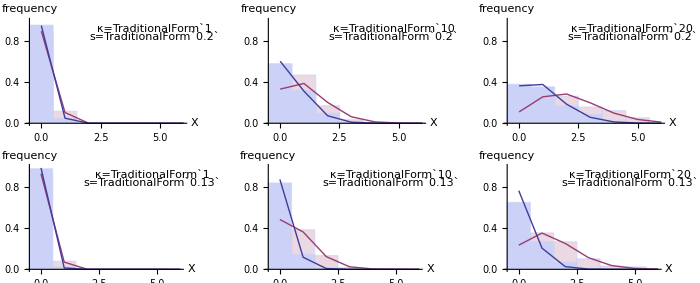

```mathematica
plotNestablishSGV[sval_,dval_,Nval_,hval_,xmax_,ks_]:=
(
params={s->sval,d->dval,N0->Nval,h->hval,B->2};

pdfgen=Simplify[PDF[BinomialDistribution[k,p],X],{0≤X≤k}];

plot=Table[
(*rescue theory*)
pdf=pdfgen/.p->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
theory=Table[{X,pdf},{X,0,xmax}];
theoryplot=ListPlot[theory,Joined->True,PlotStyle->Thick];

(*constant theory*)
pdf=pdfgen/.p->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0/.params;
theory=Table[{X,pdf},{X,0,xmax}];
theoryplotConstant=ListPlot[theory,Joined->True,PlotStyle->Directive[defaultcolors[[2]],Thick]];

(*rescue simulations*)
folder=StringForm["nestablish_SGV_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
data=Import[datadir<>ToString[folder]<>"/data/nestablish_k"<>ToString[k]<>".txt","Table"]//Flatten;
dataplot=Histogram[data,{-0.5,xmax-0.5,1},"Probability"];

(*constant simulations*)
folder=StringForm["nestablish_SGV_d``_s``",NumberForm[0,{3,2}],NumberForm[sval,{3,2}]];
data=Import[datadir<>ToString[folder]<>"/data/nestablish_k"<>ToString[k]<>".txt","Table"]//Flatten;
dataplotConstant=Histogram[data,{-0.5,xmax-0.5,1},"Probability",ChartStyle->Directive[defaultcolors[[2]],Opacity[0.2]]];

(*plot*)
Show[
dataplotConstant,dataplot,theoryplotConstant,theoryplot,
PlotRange->{0,1},
AxesLabel->{"X","frequency"},
Epilog->{
Text[StringForm["κ=``",k],Scaled@{0.8,0.9}],Text[StringForm["s=``",sval],Scaled@{0.8,0.825}]
}
],

{k,ks}
]
)

ss={0.2,0.13};
GraphicsGrid[
Table[
plotNestablishSGV[s,0.05,10^4,0.5,6,{1,10,20}],
{s,ss}
],
ImageSize->700
]
```

The probability of rescue is just the probability at least one establishes

```mathematica
PSGV=(1-Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/.X->0)
```

1-(1-ρ)^κ

Let’s check this with simulations (100 rescues for each dot, theory as lines, data as dots, rescue as solids, sweeps as open/dashed)

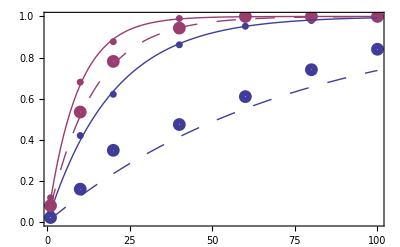

```mathematica
predictPrescue[sval_,dval_,hval_,ks_]:=
(
params={s->sval,d->dval,h->hval,B->2};
psgv=PSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
Table[{κ,psgv},{κ,ks[[1]],ks[[-1]]}]
)

getPrescue[dval_,sval_,ks_]:=
(
folder=StringForm["nestablish_SGV_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_k"<>ToString[k]<>".txt","Table"]//Flatten;
{k,100/Length[data]//N},
{k,ks}
]
)

plotPrescueSGV[svals_,dval_,Nval_,hval_,ks_]:=
(

(*rescue theory*)
theory=predictPrescue[svals[[1]],dval,hval,ks];
(*rescue theory*)
theory2=predictPrescue[svals[[2]],dval,hval,ks];
(*constant theory*)
theorySweep=predictPrescue[svals[[1]],0,hval,ks];
(*constant theory*)
theorySweep2=predictPrescue[svals[[2]],0,hval,ks];

(*rescue simulations*)
Prescue=getPrescue[dval,svals[[1]],ks];
(*rescue simulations*)
Prescue2=getPrescue[dval,svals[[2]],ks];
(*constant simulations*)
Psweep=getPrescue[0,svals[[1]],ks];
(*constant simulations*)
Psweep2=getPrescue[0,svals[[2]],ks];

Show[
ListPlot[Prescue,PlotStyle->AbsolutePointSize[5],PlotRange->{0,1}],
ListPlot[Psweep,PlotStyle->Directive[AbsolutePointSize[5],defaultcolors[[2]]]],
ListPlot[{theory,theorySweep},Joined->True,PlotStyle->Thick],
ListPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
ListPlot[Psweep2,PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]],
ListPlot[{theory2,theorySweep2},Joined->True,PlotStyle->Directive[Thick,Dashing[Large]]],
PlotRange->{0,1},
Frame->{True,True,False,False},
FrameLabel->{"Initial number of beneficial alleles"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Rotate[Text[Style["Probability of rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotPrescueSGV[{0.2,0.13},0.05,10^4,0.5,{1,10,20,40,60,80,100}]
```

The expected number of copies that establish is

```mathematica
Expectation[X,X\[Distributed]BinomialDistribution[κ,ρ]]
```

κ ρ

so the expected number that establish given rescue is

```mathematica
nSGV=1/PSGV Expectation[X,X\[Distributed]BinomialDistribution[κ,ρ]]
```

(κ ρ)/(1-(1-ρ)^κ)

Check with simulations

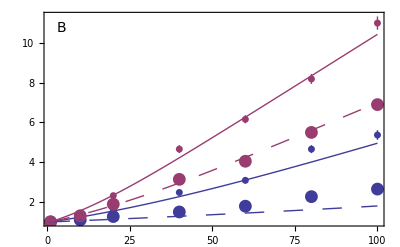

```mathematica
predictNest[sval_,dval_,hval_,ks_]:=
(
params={s->sval,d->dval,h->hval,B->2};
nsgv=nSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
Table[{κ,nsgv},{κ,ks[[1]],ks[[-1]]}]
)

getNest[dval_,sval_,ks_]:=
(
folder=StringForm["nestablish_SGV_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[
data=Import[datadir<>ToString[folder]<>"/data/nestablish_k"<>ToString[k]<>".txt","Table"]//Flatten;
data=Select[data,#>0&];
{k,Mean[data],StandardDeviation[data]/√Length[data]},
{k,ks}
]
)

plotNestablishSGVrescue[svals_,dval_,Nval_,hval_,ks_]:=
(

(*rescue theory*)
theory=predictNest[svals[[1]],dval,hval,ks];
(*rescue theory*)
theory2=predictNest[svals[[2]],dval,hval,ks];
(*constant theory*)
theorySweep=predictNest[svals[[1]],0,hval,ks];
(*constant theory*)
theorySweep2=predictNest[svals[[2]],0,hval,ks];

(*rescue simulations*)
Prescue=getNest[dval,svals[[1]],ks];
(*rescue simulations*)
Prescue2=getNest[dval,svals[[2]],ks];
(*constant simulations*)
Psweep=getNest[0,svals[[1]],ks];
(*constant simulations*)
Psweep2=getNest[0,svals[[2]],ks];

Show[
ErrorListPlot[Prescue,PlotStyle->AbsolutePointSize[5],PlotRange->{0,12}],
ErrorListPlot[Psweep,PlotStyle->Directive[AbsolutePointSize[5],defaultcolors[[2]]]],
ListPlot[{theory,theorySweep},Joined->True,PlotStyle->Thick],
ErrorListPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
ErrorListPlot[Psweep2,PlotStyle->defaultcolors[[2]],PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]],
ListPlot[{theory2,theorySweep2},Joined->True,PlotStyle->Directive[Thick,Dashing[Large]]],
Frame->{True,True,False,False},
FrameLabel->{"Initial number of beneficial alleles"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
PlotRange->All,
Epilog->{
Text[Style["B",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Lineages remaining at fixation",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotNestablishSGVrescue[{0.2,0.13},0.05,10^4,0.5,{1,10,20,40,60,80,100}]
Export[imagedir<>"NumberEstSGV.pdf",%];
```

We see that we underestimate the number that establish for weaker selection coefficients, when the beneficial allele can drift for long enough that the wildtype is rare and thus homozygotes are made, increasing establishment probabilities.

The probability that more than one copy of the beneficial allele establishes is the probability of rescue minus the probability that only one establishes

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
PSGV-(%/.X->1)//Simplify
```

1-(1-ρ)^κ-κ (1-ρ)^(-1+κ) ρ

Conditioning on rescue, the probability that more than one copy establishes is then

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
psoftSGV=(PSGV-(%/.X->1))/PSGV//Simplify
psoftSGV==1-nSGV(1-PSGV)/(1-ρ)//Simplify
```

-(-1+(1-ρ)^κ+κ (1-ρ)^(-1+κ) ρ)/(1-(1-ρ)^κ)

True

Check with simulations

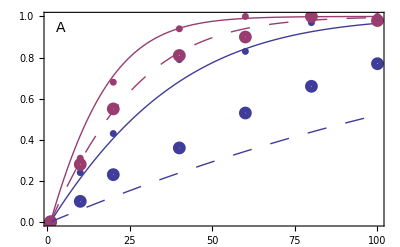

```mathematica
predictPsoft[sval_,dval_,hval_,ks_]:=
(
params={s->sval,d->dval,h->hval,B->2};
p=psoftSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
Table[{κ,p},{κ,ks[[1]],ks[[-1]]}]
)

getPsoft[dval_,sval_,ks_]:=
(
folder=StringForm["nestablish_SGV_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_k"<>ToString[k]<>".txt","Table"]//Flatten;
data=Length[Select[data,#>1&]];
{k,data/100},
{k,ks}
]
)

plotPsoftSGV[svals_,dval_,Nval_,hval_,ks_]:=
(

(*rescue theory*)
theory=predictPsoft[svals[[1]],dval,hval,ks];
(*rescue theory*)
theory2=predictPsoft[svals[[2]],dval,hval,ks];
(*constant theory*)
theorySweep=predictPsoft[svals[[1]],0,hval,ks];
(*constant theory*)
theorySweep2=predictPsoft[svals[[2]],0,hval,ks];

(*rescue simulations*)
Prescue=getPsoft[dval,svals[[1]],ks];
(*rescue simulations*)
Prescue2=getPsoft[dval,svals[[2]],ks];
(*constant simulations*)
Psweep=getPsoft[0,svals[[1]],ks];
(*constant simulations*)
Psweep2=getPsoft[0,svals[[2]],ks];

Show[
ListPlot[Prescue,PlotStyle->AbsolutePointSize[5],PlotRange->{0,12}],
ListPlot[Psweep,PlotStyle->Directive[AbsolutePointSize[5],defaultcolors[[2]]]],
ListPlot[{theory,theorySweep},Joined->True,PlotStyle->Thick],
ListPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
ListPlot[Psweep2,PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]],
ListPlot[{theory2,theorySweep2},Joined->True,PlotStyle->Directive[Thick,Dashing[Large]]],
Frame->{True,True,False,False},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
PlotRange->All,
Epilog->{
Text[Style["A",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability of a soft sweep | sweep",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotPsoftSGV[{0.2,0.13},0.05,10^4,0.5,{1,10,20,40,60,80,100}]
Export[imagedir<>"PsoftSGV.pdf",%];
```

and we see that we do a good job unless s and κ are small and d>0, which is where we underestimate the probability of establishment (due to deviations from a true branching process). If use the empirical measure of establishment probability (probability of rescue from the from the κ=1 simulations) we do much better

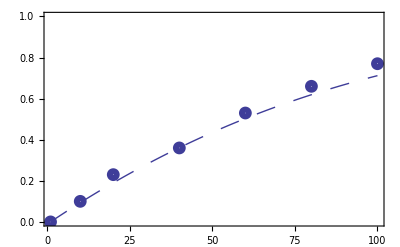

```mathematica
predictPsoftEmp[sval_,dval_,hval_,ks_]:=
(
folder=StringForm["nestablish_SGV_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
data=Import[datadir<>ToString[folder]<>"/data/nestablish_k1.txt","Table"]//Flatten;
Pest=100/Length[data]//N;
psoft=1-nSGV(1-PSGV)/(1-ρ)/.ρ->Pest;
Table[{κ,psoft},{κ,ks[[1]],ks[[-1]]}]
)

(*rescue theory*)
theory=predictPsoftEmp[0.13,0.05,0.5,{1,10,20,40,60,80,100}];
(*rescue simulations*)
Prescue=getPsoft[0.05,0.13,{1,10,20,40,60,80,100}];

Show[
ListPlot[theory,Joined->True,PlotStyle->Directive[Dashing[Large],Thick]],
ListPlot[Prescue,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
Frame->{True,True,False,False},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
PlotRangeClipping->False,
PlotRangePadding->None,
PlotRange->{0,1}
]
```

#### Effective initial allele frequency and the backward-time dynamics

Dividing the actual starting allele frequency by the probability of rescue, conditioned on rescue it is as if the beneficial allele started at frequency

```mathematica
q0rescueSGV=κ/(2N0)1/PSGV;
```

Since the probability of rescue is just the probability of sweep, this is the same in a constant population

```mathematica
q0rescueSGV;
```

Compare the predictions to simulations

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotDynamicsBackwards[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,300,letters[[i,j]],1,100,Mean],
{j,Length[ks]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

-Graphics-

#### Compare with a true branching process

Next imagine a clonally-reproducing population, which is a true branching process (when a population is below carrying capacity). The variance in reproductive success is

```mathematica
Expectation[X B,{X\[Distributed]BernoulliDistribution[V]}]/.V->w/B;
Expectation[(X B)^2,{X\[Distributed]BernoulliDistribution[V]}]-%^2/.V->w/B//Simplify
```

(B-w) w

which is lower than in the sexual model because we no longer have stochasticity in Mendelian transmission.

To compare with the sexual model, we want to keep the probability of establishment and initial frequency the same (so conditioning has the same strength). The probability of fixation is higher in the clonal model, all else being equal, because the variance is lower due to a lack of Mendelian transmission. However, starting with only half as many copies (so that the initial genotype frequency in the clonal model is the same as the initial allele frequency in the sexual model, since there are twice as many alleles as genotypes) makes the probability of fixation roughly the same for both rescue and constant populations. For example,

```mathematica
PSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.d->0/.h->0.5/.s->0.13/.B->2/.κ->10
PSGV/.ρ->pest/.v->(B-w) w/.w->(1+s h)(1-d)/.d->0/.h->0.5/.s->0.13/.B->2/.κ->5
```

0.515397

0.479392

Note that the genotype frequency dynamics in the clonal model are the same as the allele frequency dynamics in the diploid additive model under weak selection (when the advantage in the haploid model is s h=s/2)

```mathematica
q[t+1]==(q[t](1+s h)(1-d))/(q[t](1+s h)(1-d)+(1-q[t])(1-d));
Series[(q[t](1+s h)(1-d))/(q[t](1+s h)(1-d)+(1-q[t])(1-d))-q[t],{s,0,1}]//Normal;
DSolve[{D[q[t],t]==%,q[0]==q0},q[t],t]//Simplify//Flatten;
qtadditive==%/.h->1/2
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

True

The population size dynamics in the clonal model are slightly different, as the lack of homozygote mutants make for a slower recovery

```mathematica
ntadditiveClonal=DSolve[{D[n[t],t]==n[t] (q[t](1+s h)(1-d)+(1-q[t])(1-d))-n[t]/.qtadditive/.h->1/2,n[0]==N0},n[t],t]//Simplify
```

{{n[t]→ⅇ^(-d t) N0 (1+(-1+ⅇ^((s t)/2)) q0)^(1-d)}}

Backwards in time this is

```mathematica
n[t]/.ntadditiveClonal/.t->tfixadditive-τ//Simplify;
ntadditivebackClonal[τ_]:=ⅇ^(d τ) N0 (((1-q0) qf)/(q0 (1-qf)))^(-(2 d)/s) ((1-q0)(1+qf/(1-qf)ⅇ^(-(s τ)/2)))^(1- d)
FullSimplify[ntadditivebackClonal[τ]==%%,{d<1,0<q0<1}]
```

True

But let’s just look at the constant N case (so that the N dynamics are the same too).

We then see that we get the beginning of the dynamics correct (as we do for the sexual model), but tend to underestimate the mean allele frequency later in the process (again, as we do for the sexual model)

```mathematica
letters={{"A","B"},{"C","D"}};
ks={5};
ss={0.13};
GraphicsGrid[
Table[
Table[
plotDynamicsBackwardsClonal[10^4,0,ss[[i]],0.5,ks[[j]],0,0,300,letters[[i,j]],0,100,Mean],
{j,Length[ks]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

-Graphics-

#### The coalescent

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotCoalescentSims[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,2,0.01,300,0.02,letters[[i,j]],1,100],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

#### Pairwise diversity

Relative pairwise diversity

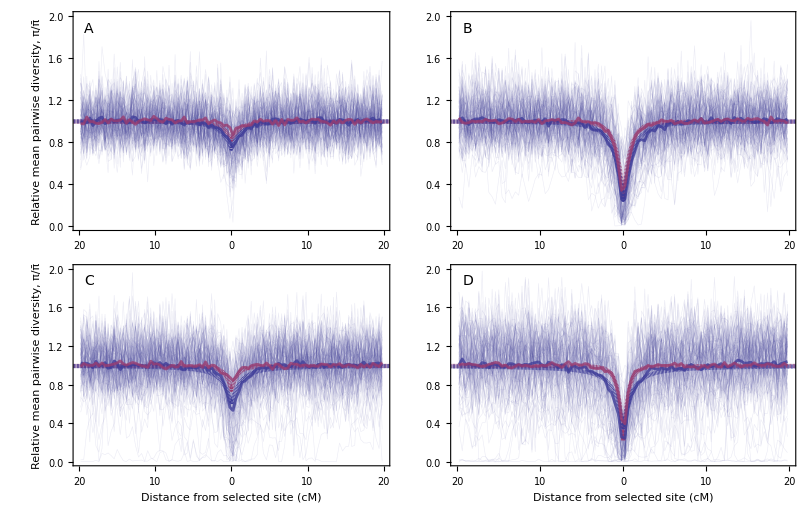

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotDiversityRelative[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],1,101],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

Absolute pairwise diversity

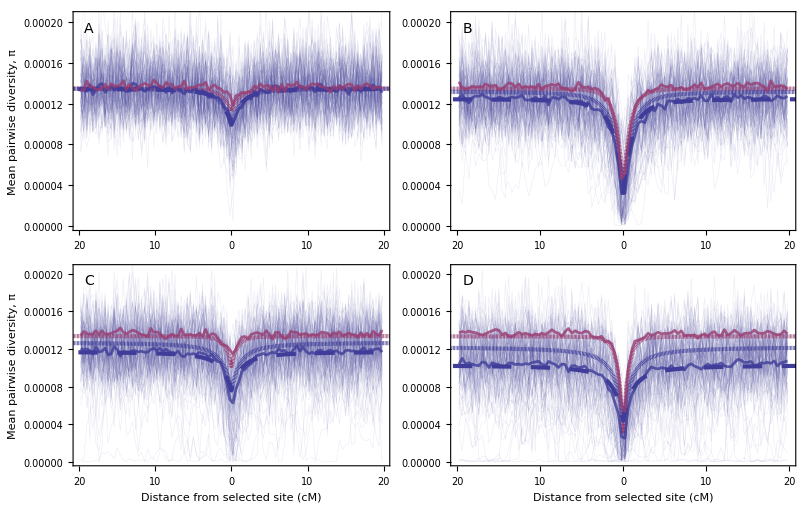

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotDiversity[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],1,101],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

#### Tajima’s D

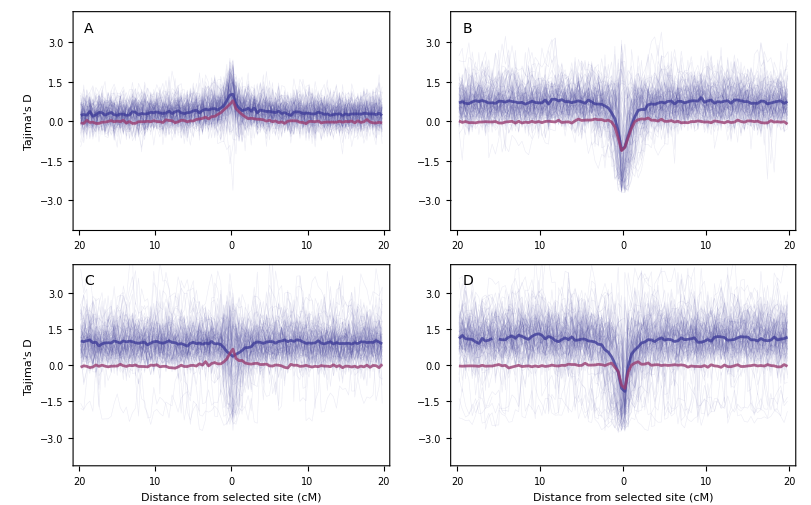

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotTajimasD[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],1],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

#### Sweep + Bottleneck (using expected bottleneck size)

We’d like to also compare the case where there is a sweep and a bottleneck, but the bottleneck is independent of the sweep. There are many ways to do it, but we’d like to concoct the bottleneck scenario such that it has the same effective population size during the sweep. Note that this does not actually make the background diversity the same as the sweeps are of different lengths (since N affects q0 and qf).

Generically, the expected population size τ generations before fixation is

```mathematica
Min[N0,ntadditiveback[τ]]
```

Min[N0,ⅇ^(d τ) N0 (((1-q0) qf)/(q0 (1-qf)))^(-(2 d)/s) ((1-q0) (1+(ⅇ^(-(s τ)/2) qf)/(1-qf)))^(2 (1-d))]

The harmonic mean population size over tfix generations is then

```mathematica
harmonicN[tfix_]:=tfix /Sum[1/Min[N0,ntadditiveback[τ]],{τ,0,tfix}](*note this should actually have started at τ=1, but the simulations have already been run and the error is small when tfix is reasonably large, which it is*)
```

And we can calculate this numerically

```mathematica
params={N0->10^4,d->0.05,s->0.2,κ->100,h->0.5,B->2};
q0=q0rescueSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+ s h)(1-d);
qf=1-1/(2N0 ρ)/.ρ->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h);
harmonicN[tfixadditive/.params]/.params

params={N0->10^4,d->0.05,s->0.2,κ->10,h->0.5,B->2};
q0=q0rescueSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+ s h)(1-d);
qf=1-1/(2N0 ρ)/.ρ->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h);
harmonicN[tfixadditive/.params]/.params

params={N0->10^4,d->0.05,s->0.13,κ->100,h->0.5,B->2};
q0=q0rescueSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+ s h)(1-d);
qf=1-1/(2N0 ρ)/.ρ->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h);
harmonicN[tfixadditive/.params]/.params

params={N0->10^4,d->0.05,s->0.13,κ->10,h->0.5,B->2};
q0=q0rescueSGV/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+ s h)(1-d);
qf=1-1/(2N0 ρ)/.ρ->pest/.v->W(3+4B-4W)/(4 Wbar^2)/.w->ϵ+1/.ϵ->1-W/Wbar/.Wbar->(1-d)(1+s)/.W->(1-d)(1+s h);
harmonicN[tfixadditive/.params]/.params

Clear[q0,qf]
```

4907.35

2945.03

2160.09

1527.53

We can now run simulations where population size is approximately constant at each of these values during the sweep, to simulate a simultaneous but independent sweep and bottleneck with the same expected effective population size during the sweep.

Compare the dynamics

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Table[
Table[
plotDynamicsBackwardsBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,300,letters[[i,j]],0,100,Mean,Ns[[i,j]]],
{j,Length[ks]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

-Graphics-

Compare the coalescent

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Table[
Table[
plotCoalescentSimsBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,2,0.01,300,0.02,letters[[i,j]],0,100,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

and right at the selected site

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Table[
Table[
plotCoalescentSimsBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,2,0,300,0.02,letters[[i,j]],0,100,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

Compare relative pairwise diversity

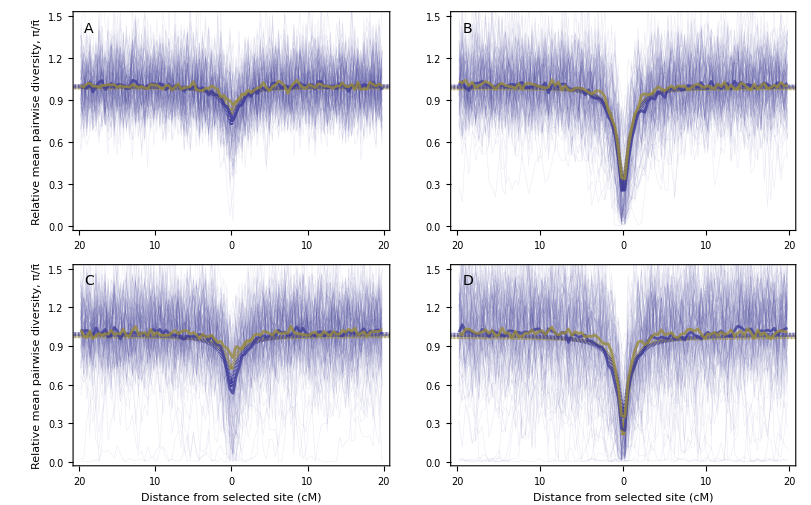

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Table[
Table[
plotDiversityRelativeBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],0,51,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

and absolute diversity (these differences mainly arise due to our overesimate of population size in the rescue scenario, which has caused us to simulate bottlenecked populations with larger effective population sizes)

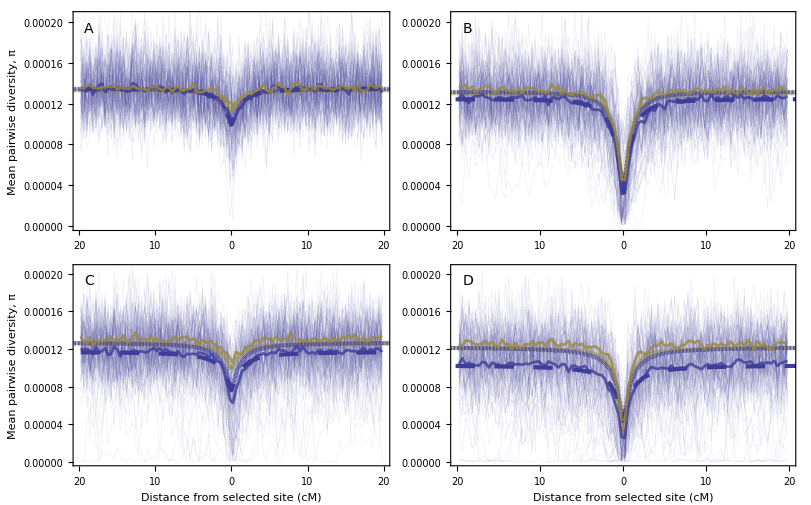

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Table[
Table[
plotDiversityBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],0,51,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

and Tajima’s D

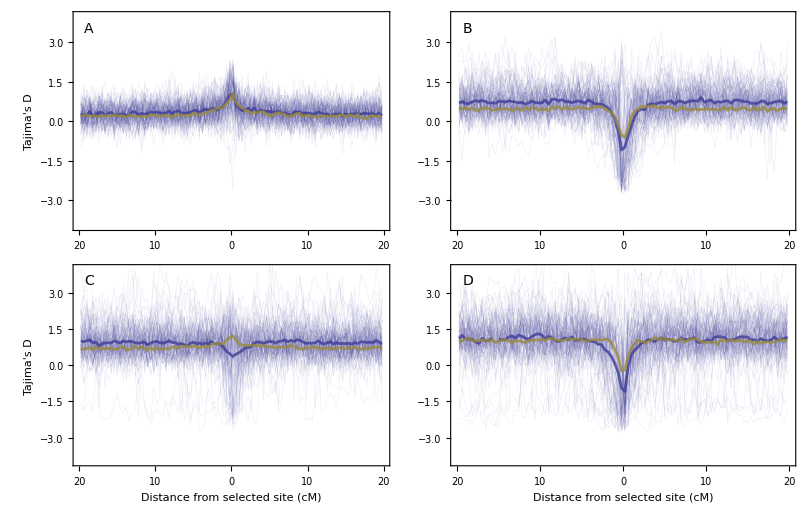

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Table[
Table[
plotTajimasDBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],0,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

And finally lets just look at the full site frequency spectrum

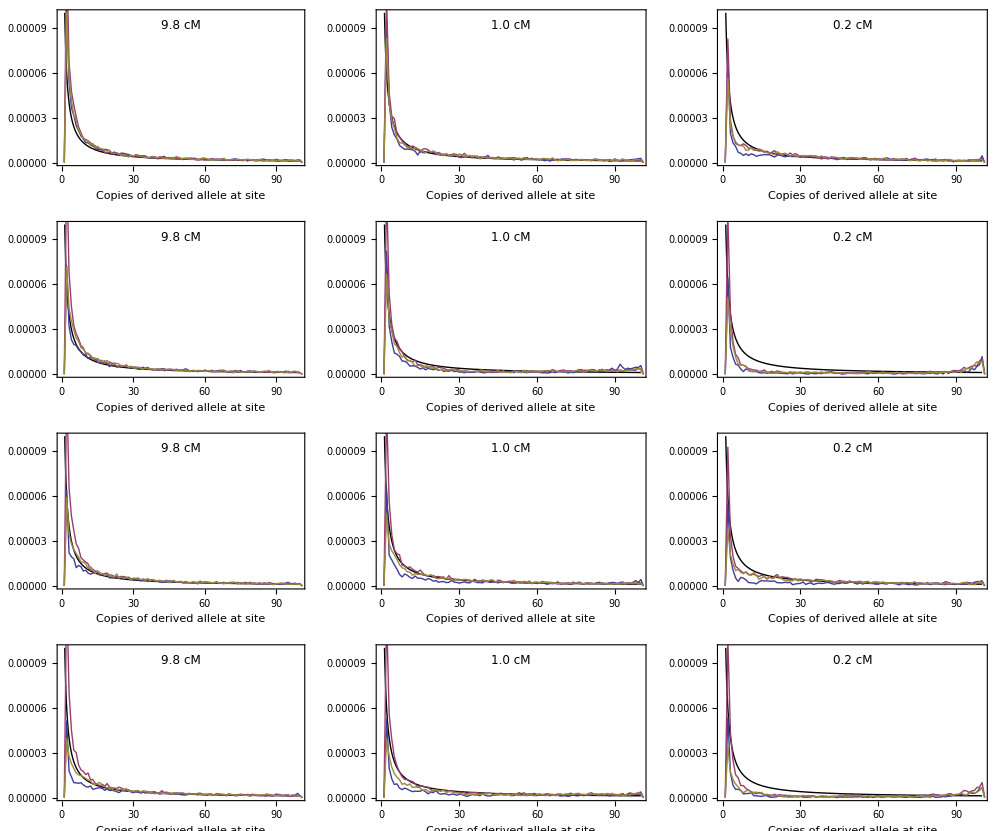

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Flatten[
Table[
Table[
plotSFS[10^4,0.05,ss[[i]],ks[[j]],0,0,100,Ns[[i,j]],6*10^-9],
{j,2}],
{i,2}],
{1,2}],
ImageSize->1000
]
```

and perhaps also on a log scale

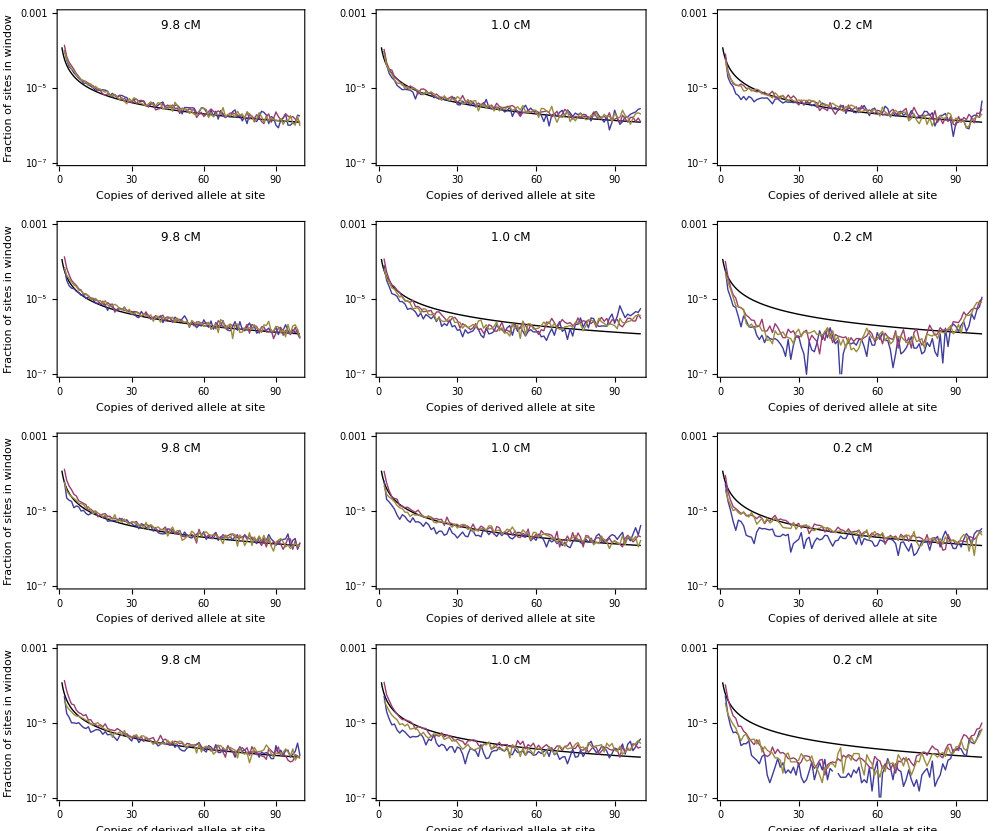

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Flatten[
Table[
Table[
plotSFSlog[10^4,0.05,ss[[i]],ks[[j]],0,0,100,Ns[[i,j]],6*10^-9,12],
{j,2}],
{i,2}],
{1,2}],
ImageSize->1000
]
```

Save one for the manuscript

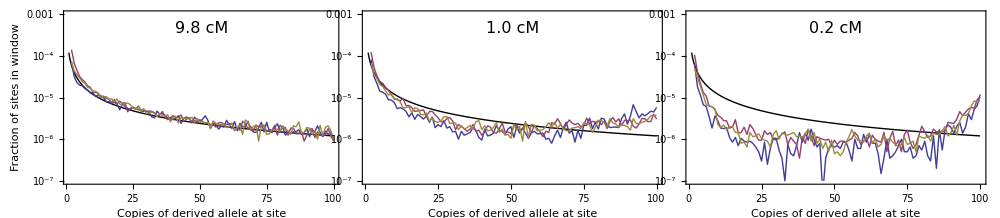

```mathematica
ks=10;
ss=0.2;
Ns=2945;
GraphicsRow[
plotSFSlog[10^4,0.05,ss,ks,0,0,100,Ns,6*10^-9,16],
ImageSize->1000,
Spacings->-30
]
Export[imagedir <> ToString[StringForm["SFS_rescue_s``_k``_bottle.pdf", ss, ks]], %];
```

And finally, let’s also take a look at linkage disequilirbium

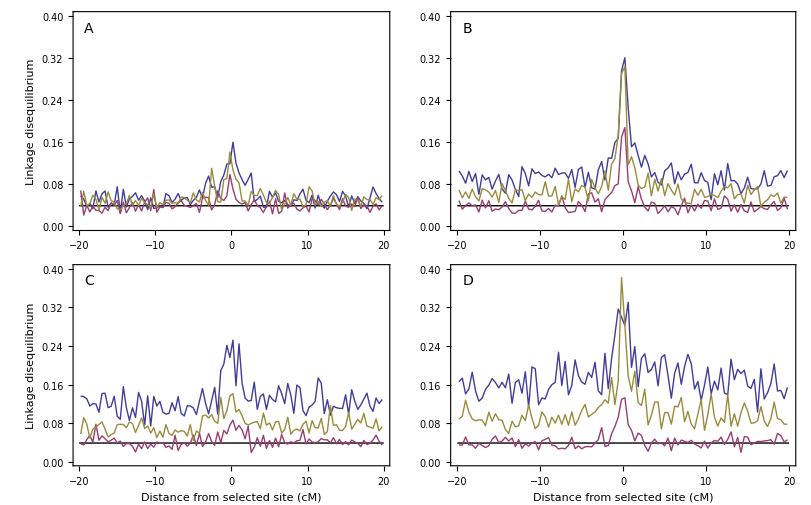

```mathematica
letters={{"A","B"},{"C","D"}};
ss={0.2,0.13};
ks={100,10};
ns={{4907,2945},{2160,1528}};
GraphicsGrid[
Table[
Table[
plotLD[10^4,0.05,ss[[i]],ks[[j]],0,0,100,ns[[i,j]],1,0.4,letters[[i,j]]],
{j,Length[ks]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

#### Sweep + Bottleneck (using observed bottleneck size)

Note that the mean harmonic mean population sizes are substantially lower than expected in rescue

```mathematica
getSimNe[10^4,0.05,0.2,100,0,0,10]
getSimNe[10^4,0.05,0.2,10,0,0,10]
getSimNe[10^4,0.05,0.13,100,0,0,10]
getSimNe[10^4,0.05,0.13,10,0,0,10]
```

3813.75

2327.15

1883.05

799.321

We therefore also simulate under these bottleneck sizes to have a more fair comparison of simulated data.

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Table[
Table[
plotDynamicsBackwardsBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,300,letters[[i,j]],0,100,Mean,Ns[[i,j]]],
{j,Length[ks]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

-Graphics-

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Table[
Table[
plotCoalescentSimsBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,2,0.01,300,0.02,letters[[i,j]],0,100,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Table[
Table[
plotCoalescentSimsBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,2,0,300,0.02,letters[[i,j]],0,100,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

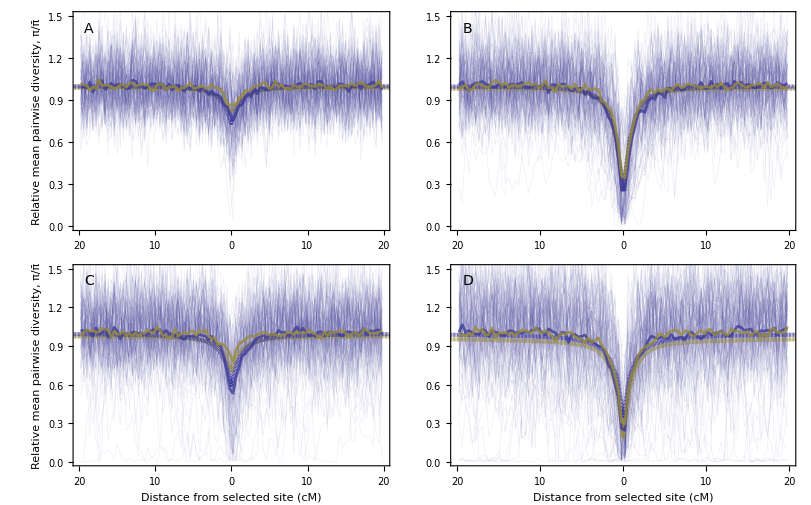

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Table[
Table[
plotDiversityRelativeBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],0,51,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

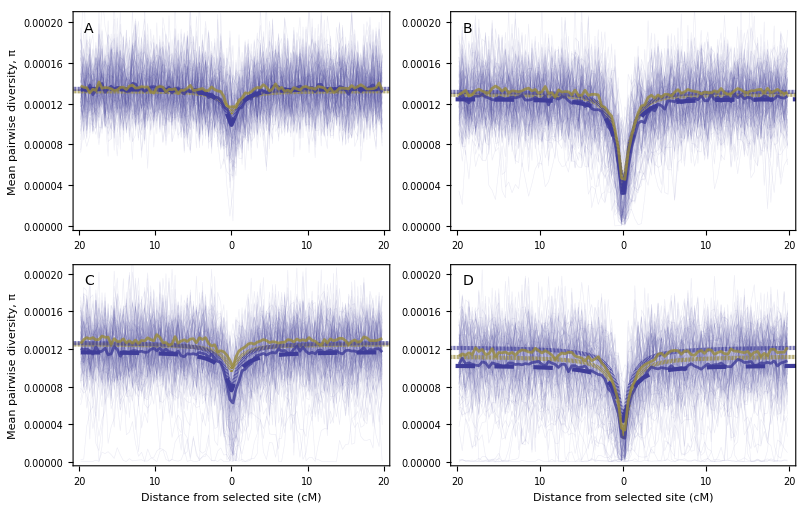

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};;
GraphicsGrid[
Table[
Table[
plotDiversityBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],0,51,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

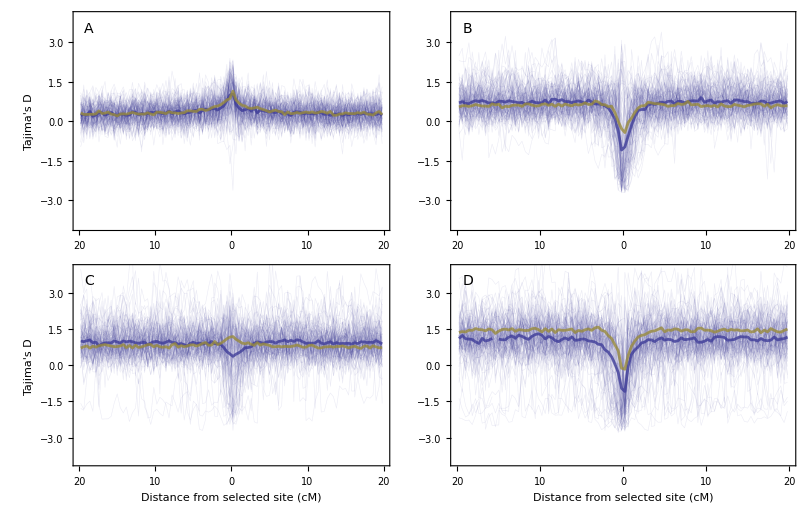

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Table[
Table[
plotTajimasDBottleneck[10^4,0.05,ss[[i]],0.5,ks[[j]],0,0,100,letters[[i,j]],0,Ns[[i,j]]],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

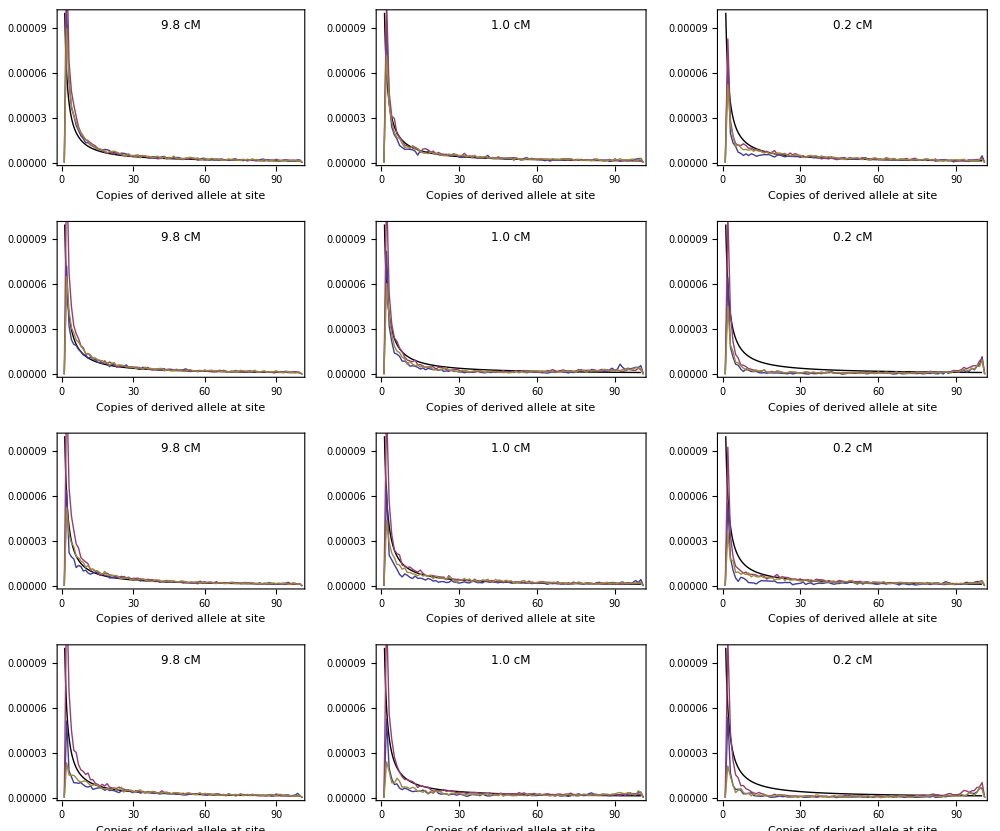

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Flatten[
Table[
Table[
plotSFS[10^4,0.05,ss[[i]],ks[[j]],0,0,100,Ns[[i,j]],6*10^-9],
{j,2}],
{i,2}],
{1,2}],
ImageSize->1000
]
```

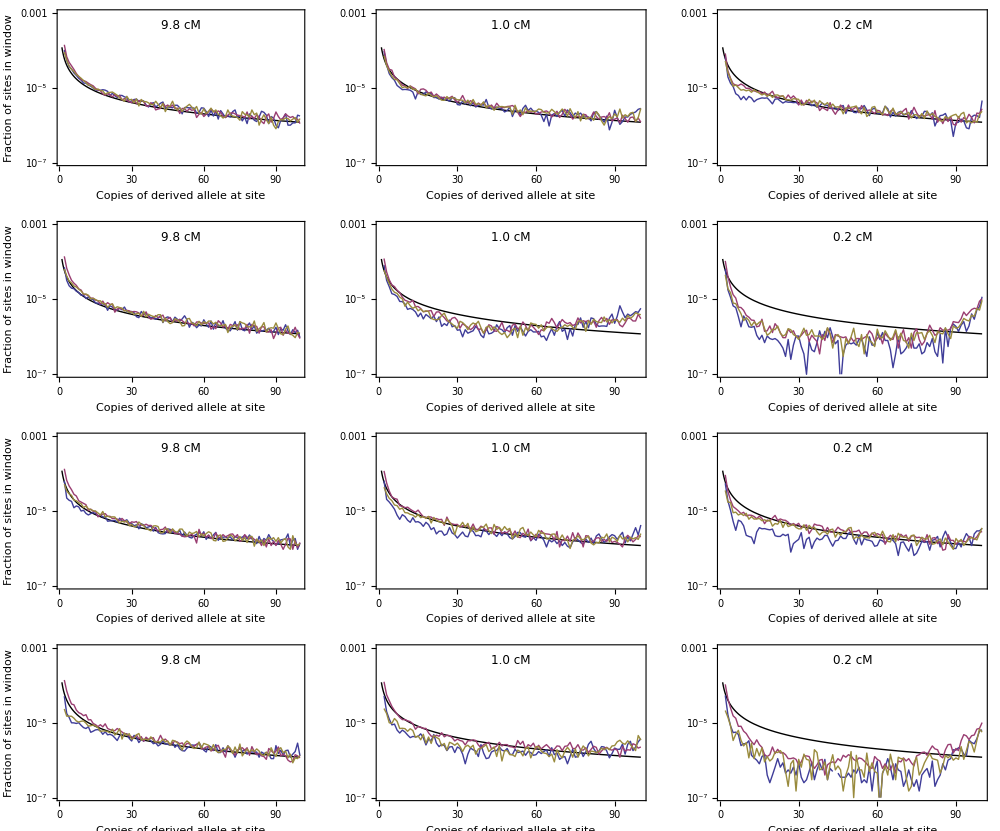

```mathematica
letters={{"A","B"},{"C","D"}};
ks={100,10};
ss={0.2,0.13};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Flatten[
Table[
Table[
plotSFSlog[10^4,0.05,ss[[i]],ks[[j]],0,0,100,Ns[[i,j]],6*10^-9,12],
{j,2}],
{i,2}],
{1,2}],
ImageSize->1000
]
```

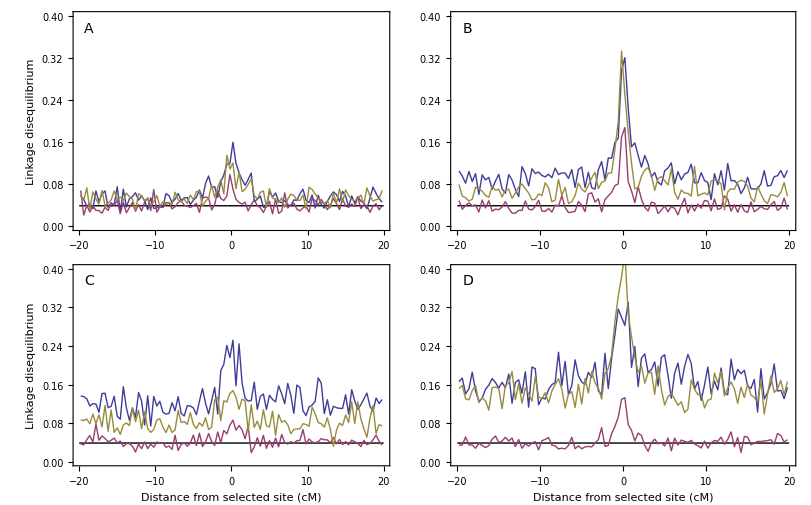

```mathematica
letters={{"A","B"},{"C","D"}};
ss={0.2,0.13};
ks={100,10};
Ns={{3814,2327},{1883,799}};
GraphicsGrid[
Table[
Table[
plotLD[10^4,0.05,ss[[i]],ks[[j]],0,0,100,Ns[[i,j]],0,0.4,letters[[i,j]]],
{j,Length[ks]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

### Rescue from de novo mutation

#### The probability of rescue and soft selective sweeps

The first successful rescue mutation arrives according to a time-inhomogeneous Poisson process with rate λ(t) = 2 N(t) u ρ, so that the probability of at it arriving by time T is 1-exp(-(∫_0)^T λ(t)dt). Therefore the probability of rescue is

```mathematica
Integrate[2N0 Exp[-d t] u ρ,{t,0,T}]//Simplify;
PDNM=Limit[1-Exp[-%],T->∞,Assumptions->d>0]
```

1-ⅇ^(-(2 N0 u ρ)/d)

Let’s check this for a few values of s and u

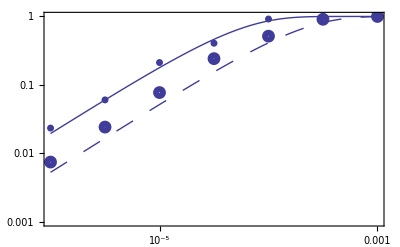

```mathematica
predictPrescue[sval_,dval_,hval_,Nval_]:=
(
params={s->sval,d->dval,h->hval,B->2,N0->Nval};
p=PDNM/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
p
)

getPrescue[dval_,sval_,us_]:=
(
folder=StringForm["nestablish_DNM_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_u"<>Which[u==10^-6,"0.000001",u==10^-5.5,"0.000003",u≥10^-5,ToString[NumberForm[u//N,{7,6}]]]<>".txt","Table"]//Flatten;
{u,100/Length[data]//N},
{u,us}
]
)

plotPrescueDNM[svals_,dval_,Nval_,hval_,us_]:=
(

(*rescue theory*)
theory=predictPrescue[svals[[1]],dval,hval,Nval];
(*rescue theory*)
theory2=predictPrescue[svals[[2]],dval,hval,Nval];

(*rescue simulations*)
Prescue=getPrescue[dval,svals[[1]],us];
(*rescue simulations*)
Prescue2=getPrescue[dval,svals[[2]],us];

Show[
ListLogLogPlot[Prescue,PlotStyle->AbsolutePointSize[5],PlotRange->{{10^-7,10^-2},{10^-4,1}}],
LogLogPlot[theory,{u,us[[1]],us[[-1]]},PlotStyle->Thick],
ListLogLogPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
LogLogPlot[theory2,{u,us[[1]],us[[-1]]},PlotStyle->Directive[Thick,Dashing[Large]]],
PlotRange->{Log@{10^-6,10^-3},Log@{10^-3,1}},
Frame->{True,True,False,False},
FrameLabel->{"Mutation rate"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Rotate[Text[Style["Probability of rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotPrescueDNM[{0.2,0.13},0.05,10^4,0.5,Table[10^(i/4),{i,-24,-11,2}]]
```

and we see that it does a pretty good job.

Establishing A alleles arrive at rate 2N[t](1-q[t])u ρ. For the first successful mutation, the population is overwhelming composed of a alleles and hence q is essentially zero at all previous times and N[t] declines exponentially at rate d. This allows us to derive the relatively simple results above. However, once A has established, the arrival of future successful mutations is complicated by the fact that q is no longer a constant and N[t] is no longer declining as a simple exponential. Now the mutation rate can be increased by an upswing in N, but this is reduced by declining numbers of a alleles, 1-q.

We can use our recursions above to write the arrival rate, λ[t], in the next generation as a function of the arrival rate in the current generation

```mathematica
2 (wbar n[t])(1-qnew)u ρ//Simplify;
%/.u->λ[t]/(2 n[t](1-q[t])ρ)//Simplify
```

-(-1+d) (1+h s q[t]) λ[t]

-(-1+d) (1+h s q[t]) λ[t]

and we see that for h≠0 this also depends on allele frequency because the A alleles prolong the persistence time of the a alleles.

When h≠0 we therefore see a non-exponential decline of a alleles due to selection in heterozygotes

```mathematica
params={s->0.2,h->0.5,N0->10^4,d->0.05,k->0,u->10.^-5,m->0};
maxrep=20;
tmax=200;
legendplace={6.5/8,1/4};

(*rescue: simulations*)
SetDirectory[NotebookDirectory[]];
folder=StringForm["K``_d``_s``_k``_u``_m``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],k/.params,NumberForm[u/.params,{6,5}],m/.params];
Clear[data]
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,maxrep}];
na=Table[(1-data[i][[2;;,3]])data[i][[2;;,2]],{i,maxrep}];

(*rescue: theory*)
q0=q0rescueDNM/.ϵ->w-1/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2;
Clear[n];
theoryq= q[t]/.qtadditive/.params;
theoryn= Min[Re[n[t]],N0]/.ntadditive/.params;

Show[
ListPlot[
 na,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[1/2],defaultcolors[[1]]],
PlotRange->All
],

Plot[
(1-theoryq)*theoryn,{t,0,tmax},
PlotStyle->Directive[AbsoluteThickness[3],Dashed,Red],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"theory"}],Scaled@legendplace],
PlotRange->All
],
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameLabel->{"Generation"},
PlotRangePadding->None,
ImagePadding->padding,
PlotRangeClipping->False,
Epilog->{
Rotate[Text[Style["Number of a alleles",labelstyle],Scaled@ylabelposition],π/2]
},
PlotRange->{0,N0/.params}
]

Clear[q0]
```

-Graphics-

but it ain’t too far off from exponential for these parameters:

```mathematica
params={s->0.2,h->0.5,N0->10^4,d->0.05,k->0,u->10.^-5,m->0};
maxrep=20;
tmax=200;
legendplace={6.5/8,1/4};

(*rescue: simulations*)
SetDirectory[NotebookDirectory[]];
folder=StringForm["K``_d``_s``_k``_u``_m``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],k/.params,NumberForm[u/.params,{6,5}],m/.params];
Clear[data]
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,maxrep}];
na=Table[(1-data[i][[2;;,3]])data[i][[2;;,2]],{i,maxrep}];

(*rescue: theory*)
theory=N0 Exp[-d t]/.params;

Show[
ListPlot[
 na,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[1/2],defaultcolors[[1]]],
PlotRange->All
],

Plot[
theory,{t,0,tmax},
PlotStyle->Directive[AbsoluteThickness[3],Dashed,Red],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"theory"}],Scaled@legendplace],
PlotRange->All
],
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameLabel->{"Generation"},
PlotRangePadding->None,
ImagePadding->padding,
PlotRangeClipping->False,
Epilog->{
Rotate[Text[Style["Number of a alleles",labelstyle],Scaled@ylabelposition],π/2]
},
PlotRange->{0,N0/.params}
]

Clear[q0]
```

-Graphics-

So we will use this exponential approximation, which will in general provide an understimate when h>0, and will get worse as h and s and u increase.

We therefore can just use the same rate of arrival of successful mutants that we used for the first mutant and the number of mutations that are expected to establish X follows a Poisson distribution

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0]
```

(2^X ⅇ^(-(2 N0 u ρ)/d) ((N0 u ρ)/d)^X)/(X!)

(2^X ⅇ^(-(2 N0 u ρ)/d) ((N0 u ρ)/d)^X)/(X!)

the distribution of X given rescue is then

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM
```

(2^X ⅇ^(-(2 N0 u ρ)/d) ((N0 u ρ)/d)^X)/((1-ⅇ^(-(2 N0 u ρ)/d)) X!)

(2^X ⅇ^(-(2 N0 u ρ)/d) ((N0 u ρ)/d)^X)/((1-ⅇ^(-(2 N0 u ρ)/d)) X!)

which has expectation

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM;
nDNM=Sum[% X,{X,1,∞}];
Simplify[nDNM==(-Log[1-PDNM])/PDNM,{N0>0,u>0,ρ>0,d>0}]
```

True

True

And we can also derive the probability of a soft sweep given rescue

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM;
psoftDNM=1-(%/.X->1)//Simplify;
FullSimplify[psoftDNM==1-nDNM(1-PDNM),{N0>0,u>0,ρ>0,d>0}]
```

True

True

which is essentially the results of Wilson et al 2017 Genetics, who modeled a haploid population, when we ignore density-dependence (just a slight change to the Poisson rate in their equation 7 due to diploidy and our life-cycle).

Let’s look at the probability of a soft sweep given rescue across a range of mutation rates for these two selection coefficients

```mathematica
predictPsoft[sval_,dval_,hval_,Nval_]:=
(
params={s->sval,d->dval,h->hval,B->2,N0->Nval};
p=psoftDNM/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
p
)

getPsoft[dval_,sval_,us_]:=
(
folder=StringForm["nestablish_DNM_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_u"<>Which[u==10^-6,"0.000001",u==10^-5.75,"0.000002",u==10^-5.5,"0.000003",u==10^-5.25,"0.000006",u≥10^-5,ToString[NumberForm[u//N,{7,6}]]]<>".txt","Table"]//Flatten;
data=Length[Select[data,#>1&]];
{u,data/100},
{u,us}
]
)

plotPsoftDNM[svals_,dval_,Nval_,hval_,uss_]:=
(

(*rescue theory*)
theory=predictPsoft[svals[[1]],dval,hval,Nval];
(*rescue theory*)
theory2=predictPsoft[svals[[2]],dval,hval,Nval];
(*constant theory*)
theorySweep=1-Product[j/(j+θ),{j,2N0-1}]/.θ->2N0 NeN u/.NeN->4/7/.N0->Nval//N;

(*rescue simulations*)
Prescue=getPsoft[dval,svals[[1]],uss[[1]]];
(*rescue simulations*)
Prescue2=getPsoft[dval,svals[[2]],uss[[1]]];
(*constant simulations*)
Psweep=getPsoft[0,svals[[1]],uss[[1]]];
(*constant simulations*)
Psweep2=getPsoft[0,svals[[2]],uss[[2]]];

Show[
LogLinearPlot[theory,{u,uss[[1,1]],uss[[1,-1]]},PlotStyle->Thick,FrameTicks->{{Automatic,Automatic},{{{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"}},Automatic}}],
ListLogLinearPlot[Prescue,PlotStyle->AbsolutePointSize[5],PlotRange->{0,1}],
ListLogLinearPlot[Psweep,PlotStyle->Directive[AbsolutePointSize[5],defaultcolors[[2]]]],
LogLinearPlot[{,theorySweep},{u,uss[[1,1]],uss[[1,-1]]},PlotStyle->Directive[Thick,Dotted]],
ListLogLinearPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
ListLogLinearPlot[Psweep2,PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]],
LogLinearPlot[theory2,{u,uss[[1,1]],uss[[1,-1]]},PlotStyle->Directive[Thick,Dashing[Large]]],
PlotRange->{0,1},
Frame->{True,True,False,False},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
PlotRange->All,
Epilog->{
Text[Style["A",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability of a soft sweep | sweep",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotPsoftDNM[{0.2,0.13},0.05,10^4,0.5,{Table[10^(i/4),{i,-24,-11,2}],Table[10^(i/4),{i,-23,-12,2}]}]
Export[imagedir<>"PsoftDNM.pdf",%];
```

-Graphics-

and the expected number of copies of the beneficial allele that establish given rescue

```mathematica
predictNest[sval_,dval_,hval_,Nval_]:=
(
params={s->sval,d->dval,h->hval,B->2,N0->Nval};
n=nDNM/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
n
)

getNest[dval_,sval_,us_]:=
(
folder=StringForm["nestablish_DNM_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_u"<>Which[u==10^-6,"0.000001",u==10^-5.75,"0.000002",u==10^-5.5,"0.000003",u==10^-5.25,"0.000006",u≥10^-5,ToString[NumberForm[u//N,{7,6}]]]<>".txt","Table"]//Flatten;
data=Select[data,#>0&];
{u,Mean[data],StandardDeviation[data]/√Length[data]},
{u,us}
]
)

plotNestablishDNMrescue[svals_,dval_,Nval_,hval_,uss_]:=
(

(*rescue theory*)
theory=predictNest[svals[[1]],dval,hval,Nval];
(*rescue theory*)
theory2=predictNest[svals[[2]],dval,hval,Nval];
(*constant theory*)
theorySweep=Sum[θ/(j-1+θ),{j,2N0}]/.θ->2N0 NeN u/.N0->Nval/.NeN->4/7;

(*rescue simulations*)
Prescue=getNest[dval,svals[[1]],uss[[1]]];
(*rescue simulations*)
Prescue2=getNest[dval,svals[[2]],uss[[1]]];
(*constant simulations*)
Psweep=getNest[0,svals[[1]],uss[[1]]];
(*constant simulations*)
Psweep2=getNest[0,svals[[2]],uss[[2]]];

Show[
LogLogPlot[theory,{u,uss[[1,1]],uss[[1,-1]]},PlotStyle->Thick,PlotRange->{{10^-6,10^-3},{1,1000}},FrameTicks->{{Automatic,Automatic},{{{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"}},Automatic}}
],
ErrorListPlot[Prescue,PlotStyle->AbsolutePointSize[5]]/.{x_Real,y_Real}->{Log@x,Log@y},
ErrorListPlot[Psweep,PlotStyle->Directive[AbsolutePointSize[5],defaultcolors[[2]]]]/.{x_Real,y_Real}->{Log@x,Log@y},
ErrorListPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]]/.{x_Real,y_Real}->{Log@x,Log@y},
ErrorListPlot[Psweep2,PlotStyle->defaultcolors[[2]],PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]]/.{x_Real,y_Real}->{Log@x,Log@y},
LogLogPlot[{,theorySweep},{u,uss[[1,1]],uss[[1,-1]]},PlotStyle->Directive[Thick,Dotted]],
LogLogPlot[theory2,{u,uss[[1,1]],uss[[1,-1]]},PlotStyle->Directive[Thick,Dashing[Large]]],
(*PlotRange->Log@{{10^-7,10^-2},{1,100}},*)
Frame->{True,True,False,False},
FrameLabel->{"Mutation rate at selected site"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
PlotRange->All,
Epilog->{
Text[Style["B",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Number of unique lineages at fixation",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotNestablishDNMrescue[{0.2,0.13},0.05,10^4,0.5,{Table[10^(i/4),{i,-24,-11,2}],Table[10^(i/4),{i,-23,-12,2}]}]
Export[imagedir<>"NumberEstDNM.pdf",%];
```

-Graphics-

#### Effective initial allele frequency and the backward-time dynamics

Taking the derivative of the approximate cumulative distribution function with respect to T and dividing by the probability of rescue gives the PDF of waiting times until the first rescue mutation

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t
```

(2 ⅇ^(-d t-(2 (1-ⅇ^(-d t)) N0 u ρ)/d) N0 u ρ)/(1-ⅇ^(-(2 N0 u ρ)/d))

This has mean

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
Integrate[t %,{t,0,∞},Assumptions->d>0]
```

(EulerGamma+Gamma[0,-(2 N0 u ρ)/d]+Log[-(2 N0 u ρ)/d])/(d-d ⅇ^((2 N0 u ρ)/d))

and standard deviation

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
(Integrate[t^2 %,{t,0,∞},Assumptions->d>0]-Integrate[t %,{t,0,∞},Assumptions->d>0]^2)^(1/2)
```

√(1/d^3 2 N0 u ρ (-1+Coth[(N0 u ρ)/d]) HypergeometricPFQ[{1,1,1},{2,2,2},(2 N0 u ρ)/d]-(EulerGamma+Gamma[0,-(2 N0 u ρ)/d]+Log[-(2 N0 u ρ)/d])^2/(d-d ⅇ^((2 N0 u ρ)/d))^2)

If we consider a frequency of 1/2N0ρ as the time of arrival (given that will quickly be reached or the mutation lost), we can compare these estimates with simulations

```mathematica
timeDNM[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];
allp=Table[data[i][[2;;,3]],{i,nreps}];
threshold=1/(2N0 ρ)/.ρ->pest/.v->(3+4 B-4 w) w/4/.w->(1+s h)(1-d)/.B->2/.N0->Nval/.d->dval/.s->sval/.h->hval/.u->uval;
data=Table[Position[allp[[i]],x_/;x>threshold][[1]]//First,{i,Length[allp]}];
theory=(2 ⅇ^(-d t-(2 (1-ⅇ^(-d t)) N0 u ρ)/d) N0 u ρ)/(1-ⅇ^(-(2 N0 u ρ)/d))/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.h->hval/.N0->Nval/.d->dval/.s->sval/.u->uval;
mean=(EulerGamma+Gamma[0,-(2 N0 u ρ)/d]+Log[-(2 N0 u ρ)/d])/(d-d ⅇ^((2 N0 u ρ)/d))/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.h->hval/.N0->Nval/.d->dval/.s->sval/.u->uval;
sd=√(1/d^3 2 N0 u ρ (-1+Coth[(N0 u ρ)/d]) HypergeometricPFQ[{1,1,1},{2,2,2},(2 N0 u ρ)/d]-(EulerGamma+Gamma[0,-(2 N0 u ρ)/d]+Log[-(2 N0 u ρ)/d])^2/(d-d ⅇ^((2 N0 u ρ)/d))^2)/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.h->hval/.N0->Nval/.d->dval/.s->sval/.u->uval;
Show[
Plot[theory,{t,0,100},PlotRange->All],
Histogram[data,Automatic,"PDF",PlotRange->All],
Plot[theory,{t,0,100}],
Frame->{True,True,False,False},
FrameLabel->{"time of arrival", "frequency"},
Epilog->{
Text[StringForm["s=``, u=``",sval,uval],Scaled@{0.8,0.2}],
Text[StringForm["(t̄)_true=``±``",Mean[data]//N,StandardDeviation[data]//N],Scaled@{0.8,0.4}],
Text[StringForm["(t̄)_app=``±``",Re[mean]//N,Re[sd]//N],Scaled@{0.8,0.5}]
}
]
)

GraphicsColumn[{
timeDNM[10^4,0.05,0.13,0.5,0,10^-5//N,0,100],
timeDNM[10^4,0.05,0.2,0.5,0,10^-5//N,0,100],
timeDNM[10^4,0.05,0.13,0.5,0,10^-4//N,0,100],
timeDNM[10^4,0.05,0.2,0.5,0,10^-4//N,0,100]
},
ImageSize->400
]
```

-Graphics-

We see a decent correspondance with the means, except maybe in the first case where the realized mean arrival time is a bit later than expected.

Let’s call c the expected number of mutations, then the pdf can be written

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)
```

(c d ⅇ^(-c (1-ⅇ^(-d t))-d t))/(1-ⅇ^-c)

The first establishing mutation, arriving at time τ, will grow in number nearly exponentially, at rate ϵ =w-1= (1 + s h)(1-d)-1, while it is rare. And given that it establishes will very quickly reach 1/ρ copies. Integrating over the arrival times τ then gives the expected number of copies t generations after environmental change

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)/.t->τ;
Integrate[(Exp[ϵ(t-τ)]/ρ)%,{τ,0,∞},Assumptions->{d>0,ρ>0,ϵ>0}]
```

((-c)^(-ϵ/d) ⅇ^(t ϵ) (-Gamma[(d+ϵ)/d]+Gamma[(d+ϵ)/d,-c]))/((-1+ⅇ^c) ρ)

so that it is as if the initial frequency was

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)/.t->τ;
Integrate[( 1/ρ)Exp[ϵ(t-τ)]%,{τ,0,∞},Assumptions->{d>0,ρ>0,ϵ>0}];
1/(2N0)%/.t->0//Simplify;
q0rescueDNM=%/.c->u 2N0 ρ/d
Simplify[%==1/(2 N0 ρ)((1-PDNM)(Gamma[1+ϵ/d,Log[1-PDNM]]-Gamma[1+ϵ/d]) )/(PDNM Log[1-PDNM]^(ϵ/d)),{N0>0,u>0,ρ>0,d>0,ϵ>0}]
```

(2^(-1-ϵ/d) (-(N0 u ρ)/d)^(-ϵ/d) (-Gamma[(d+ϵ)/d]+Gamma[(d+ϵ)/d,-(2 N0 u ρ)/d]))/((-1+ⅇ^((2 N0 u ρ)/d)) N0 ρ)

True

When the expected number of rescue mutations, c, is very small this reduces to the Orr & Unckless 2014 result (where the waiting time is independent of the mutation rate, the last term in their equation 19)

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)/.t->τ;
Integrate[(Exp[ϵ(t-τ)]/ρ)%,{τ,0,∞},Assumptions->{d>0,ρ>0,ϵ>0}];
Simplify[Series[%,{c,0,0}]//Normal,{c>0,ρ>0,d>0,ϵ>0}]
%/.ϵ->s -d/.ρ->2(s-d)/.d->r//Simplify
```

(d ⅇ^(t ϵ))/(d ρ+ϵ ρ)

-(ⅇ^(-r t+s t) r)/(2 r s-2 s^2)

In a population of constant size the waiting time for an allele that fixes is exponential

```mathematica
Simplify[PDF[ExponentialDistribution[λ],τ],τ>0]/.λ->2N0 u ρ
```

2 ⅇ^(-2 N0 u ρ τ) N0 u ρ

which has mean 1/λ and standard deviation 1/λ.

Using 1/(2N0 ρ) as the initial frequency (as for the case of rescue) we can compare this to simulations

```mathematica
timeDNMconstant[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_]:=
(
folder=StringForm["K``_d``_s``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];
allp=Table[data[i][[2;;,3]],{i,nreps}];
threshold=1/(2N0 ρ)/.ρ->pest/.v->(3+4 B-4 w) w/4/.w->(1+s h)(1-d)/.B->2/.N0->Nval/.d->dval/.s->sval/.h->hval/.u->uval;
data=Table[Position[allp[[i]],x_/;x>threshold][[1]]//First,{i,Length[allp]}];
theory=ⅇ^(-λ t) λ/.λ->2N0 u ρ/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.h->hval/.N0->Nval/.d->dval/.s->sval/.u->uval;
mean=1/λ/.λ->2N0 u ρ/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.h->hval/.N0->Nval/.d->dval/.s->sval/.u->uval;
sd=1/λ/.λ->2N0 u ρ/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.h->hval/.N0->Nval/.d->dval/.s->sval/.u->uval;
Show[
Plot[theory,{t,0,200},PlotRange->{0,All}],
Histogram[data,Automatic,"PDF",PlotRange->All],
Plot[theory,{t,0,200}],
Frame->{True,True,False,False},
FrameLabel->{"time of arrival", "frequency"},
Epilog->{
Text[StringForm["s=``, u=``",sval,uval],Scaled@{0.8,0.2}],
Text[StringForm["(t̄)_true=``±``",Mean[data]//N,StandardDeviation[data]//N],Scaled@{0.8,0.4}],
Text[StringForm["(t̄)_app=``±``",Re[mean]//N,Re[sd]//N],Scaled@{0.8,0.5}]
}
]
)

GraphicsColumn[{
timeDNMconstant[10^4,0.0,0.13,0.5,0,10^-5//N,0,100],
timeDNMconstant[10^4,0.0,0.2,0.5,0,10^-5//N,0,100],
timeDNMconstant[10^4,0.0,0.13,0.5,0,10^-4//N,0,100],
timeDNMconstant[10^4,0.0,0.2,0.5,0,10^-4//N,0,100]
},
ImageSize->400
]
```

-Graphics-

Given the successful allele arises at time τ and fixes, it will very quickly increase to frequency 1/(2N0ρ). The frequency will then increase at rate ϵ while still rare, so that the frequency at time t is expected to be

```mathematica
Simplify[PDF[ExponentialDistribution[λ],τ],τ>0];
Integrate[(1/(2N0 ρ))Exp[ϵ(t-τ)]%,{τ,0,∞},Assumptions->{λ>0,ρ>0,ϵ>0}]/.λ->2N0 u ρ//Simplify
```

(ⅇ^(t ϵ) u)/(ϵ+2 N0 u ρ)

Such that it is as if the frequency at time 0 was

```mathematica
Simplify[PDF[ExponentialDistribution[λ],τ],τ>0];
Integrate[(1/(2N0 ρ))Exp[ϵ(t-τ)]%,{τ,0,∞},Assumptions->{λ>0,ρ>0,ϵ>0}]/.λ->2N0 u ρ//Simplify;
%/.t->0
```

u/(ϵ+2 N0 u ρ)

However, given that the population size is expected to be constant and the allele frequency dynamics backwards in time do not depend on the time the sweep starts, we need only concern ourselves with the effective initial frequency at the time of establishment

```mathematica
q0sweepDNM=1/(2N0 ρ);
```

Plot the backward-time dynamics

```mathematica
letters={{"A","B"},{"C","D"}};
us={10.^-4,10.^-5};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotDynamicsBackwards[10^4,0.05,ss[[i]],0.5,0,us[[j]],0,300,letters[[i,j]],1,100,Median],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

#### The coalescent

```mathematica
letters={{"A","B"},{"C","D"}};
us={10.^-4,10.^-5};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotCoalescentSims[10^4,0.05,ss[[i]],0.5,0,us[[j]],0,2,0.01,300,0.02,letters[[i,j]],1,100],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

#### Pairwise diversity

```mathematica
letters={{"A","B"},{"C","D"}};
us={10.^-4,10.^-5};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotDiversityRelative[10^4,0.05,ss[[i]],0.5,0,us[[j]],0,100,letters[[i,j]],1,101],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

```mathematica
letters={{"A","B"},{"C","D"}};
us={10.^-4,10.^-5};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotDiversity[10^4,0.05,ss[[i]],0.5,0,us[[j]],0,100,letters[[i,j]],0,51],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

#### Tajima’s D

```mathematica
letters={{"A","B"},{"C","D"}};
us={10.^-4,10.^-5};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotTajimasD[10^4,0.05,ss[[i]],0.5,0,us[[j]],0,100,letters[[i,j]],1],
{j,2}],
{i,2}],
Spacings->{0,0}
]
```

-Graphics-

### Rescue from migration

#### The probability of rescue and soft selective sweeps

If we assume beneficial alleles arrive at constant rate m then the probability a successful one has not arrived by time t is

```mathematica
PDF[PoissonDistribution[m ρ t],X]/.X->0
```

ⅇ^(-m t ρ)

The population is expected to go extinct in

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten
```

{t→Log[N0]/d}

generations and thus the probability of rescue by a migrant allele is roughly the probability at least one has established by then

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten;
PMIG=1-PDF[PoissonDistribution[m ρ t],X]/.X->0/.%
```

1-N0^(-(m ρ)/d)

Check with simulations

```mathematica
predictPrescue[sval_,dval_,hval_,Nval_]:=
(
params={s->sval,d->dval,h->hval,B->2,N0->Nval};
p=PMIG/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
p
)

getPrescue[dval_,sval_,ms_]:=
(
folder=StringForm["nestablish_MIG_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_m"<>ToString[NumberForm[m,{4,3}]]<>".txt","Table"]//Flatten;
{m,100/Length[data]//N},
{m,ms}
]
)

plotPrescueMIG[svals_,dval_,Nval_,hval_,ms1_,ms2_]:=
(

(*rescue theory*)
theory=predictPrescue[svals[[1]],dval,hval,Nval];
(*rescue theory*)
theory2=predictPrescue[svals[[2]],dval,hval,Nval];

(*rescue simulations*)
Prescue=getPrescue[dval,svals[[1]],ms1];
(*rescue simulations*)
Prescue2=getPrescue[dval,svals[[2]],ms2];

Show[
ListLogLogPlot[Prescue,PlotStyle->AbsolutePointSize[5],PlotRange->{{10^-2,10^0},{10^-2,1}}],
LogLogPlot[theory,{m,ms1[[1]],1},PlotStyle->Thick],
ListLogLogPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
LogLogPlot[theory2,{m,ms1[[1]],1},PlotStyle->Directive[Thick,Dashing[Large]]],
PlotRange->Log@{{10^-2,10^0},{10^-2,1}},
Frame->{True,True,False,False},
FrameLabel->{"Migration rate"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Rotate[Text[Style["Probability of rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotPrescueMIG[{0.2,0.13},0.05,10^4,0.5,Table[10^(i/10),{i,-19,0,4}]//N,Table[10^(i/10),{i,-17,0,4}]//N]
```

-Graphics-

Note that, if ne/n is constant, so is the ratio of migration to coalescence

```mathematica
pmig[k,τ]/(pcoal[k,τ]/.n[τ]->ne[τ])/.ne[τ]->NeN n[τ]
```

(2 m NeN)/(-1+k)

We can therefore use Ewen’s sampling formula to get the distribution of migrant haplotypes among a sample, replacing θ with

```mathematica
Solve[(2 ne[τ] x[τ] pmut[k,τ]/.u->θ/(4ne[τ])/.x[τ]->0)==(2 ne[τ] x[τ]pmig[k,τ]/.n[τ]->ne[τ]/NeN),θ]//Flatten
```

{θ→2 m NeN}

For example, the expected number of migrant haplotypes found in a sample of size n is (Ewens 2004 p 336)

```mathematica
nMIG=Sum[θ/(j-1+θ),{j,k}]
```

-θ PolyGamma[0,θ]+θ PolyGamma[0,k+θ]

Try that out with simulation data

```mathematica
predictNest[nval_]:=
(
params={k->nval,θ->2 m NeN};
nest=nMIG/.params/.NeN->4/7;
nest
)

getNest[dval_,sval_,ms_]:=
(
folder=StringForm["nestablish_MIG_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_m"<>ToString[NumberForm[m,{4,3}]]<>".txt","Table"]//Flatten;
data=Select[data,#>0&];
{m,Mean[data],StandardDeviation[data]/√Length[data]},
{m,ms}
]
)

plotNestablishMIGrescue[svals_,dval_,Nval_,mss_]:=
(

(*rescue theory*)
theory=predictNest[2Nval];

(*constant simulations*)
Psweep=getNest[0,svals[[1]],mss[[1]]];
(*rescue simulations*)
Prescue=getNest[dval,svals[[1]],mss[[2]]];
(*constant simulations*)
Psweep2=getNest[0,svals[[2]],mss[[3]]];
(*rescue simulations*)
Prescue2=getNest[dval,svals[[2]],mss[[4]]];

Show[
LogLogPlot[theory,{m,0.01,1},PlotStyle->Directive[Purple,Thick,Opacity[0.5]],PlotRange->{{10^-2,1},{1,15}}
],
ErrorListPlot[Prescue,PlotStyle->AbsolutePointSize[5]]/.{x_Real,y_Real}->{Log@x,Log@y},
ErrorListPlot[Psweep,PlotStyle->Directive[AbsolutePointSize[5],defaultcolors[[2]]]]/.{x_Real,y_Real}->{Log@x,Log@y},
ErrorListPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]]/.{x_Real,y_Real}->{Log@x,Log@y},
ErrorListPlot[Psweep2,PlotStyle->defaultcolors[[2]],PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]]/.{x_Real,y_Real}->{Log@x,Log@y},
(*PlotRange->Log@{{10^-7,10^-2},{1,100}},*)
Frame->{True,True,False,False},
FrameLabel->{"Migration rate"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Text[Style["B",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Number of unique lineages at fixation",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotNestablishMIGrescue[{0.2,0.13},0.05,10^4,{Table[10^(i/10),{i,-20,0,4}],Table[10^(i/10),{i,-19,0,4}],Table[10^(i/10),{i,-18,0,4}],Table[10^(i/10),{i,-17,0,4}]}//N]
Export[imagedir<>"NumberEstMIG.pdf",%];
```

-Graphics-

And the probability of a soft sweep is

```mathematica
psoftMIG=1-Product[j/(j+θ),{j,k-1}]
```

1-((-1+k)!)/Pochhammer[1+θ,-1+k]

and try that with simulation data

```mathematica
predictPsoft[nval_]:=
(
params={k->nval,θ->2m NeN };
p=psoftMIG/.params/.NeN->4/7;
p//N
)

getPsoft[dval_,sval_,ms_]:=
(
folder=StringForm["nestablish_MIG_d``_s``",NumberForm[dval,{3,2}],NumberForm[sval,{3,2}]];
Table[data=Import[datadir<>ToString[folder]<>"/data/nestablish_m"<>ToString[NumberForm[m,{4,3}]]<>".txt","Table"]//Flatten;
data=Length[Select[data,#>1&]];
{m,data/100},
{m,ms}
]
)

plotPsoftMIG[Nval_,dval_,svals_,mss_]:=
(

(*theory*)
theory=predictPsoft[2Nval];

(*constant simulations*)
Psweep=getPsoft[0,svals[[1]],mss[[1]]];
(*rescue simulations*)
Prescue=getPsoft[dval,svals[[1]],mss[[2]]];
(*constant simulations*)
Psweep2=getPsoft[0,svals[[2]],mss[[3]]];
(*rescue simulations*)
Prescue2=getPsoft[dval,svals[[2]],mss[[4]]];


Show[
LogLinearPlot[{,,theory},{m,0.01,1},PlotStyle->Directive[Purple,Thick,Opacity[0.5]],PlotRange->{0,1}],
ListLogLinearPlot[Prescue,PlotStyle->AbsolutePointSize[5],PlotRange->{0,1}],
ListLogLinearPlot[Psweep,PlotStyle->Directive[AbsolutePointSize[5],defaultcolors[[2]]]],
ListLogLinearPlot[Prescue2,PlotMarkers->Graphics[{Thickness[0.4],Circle[]},ImageSize->6]],
ListLogLinearPlot[Psweep2,PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]],
(*PlotRange->{Log@{10^-2,1},{0,1}},*)
Frame->{True,True,False,False},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
PlotRange->All,
Epilog->{
Text[Style["A",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability of a soft sweep | sweep",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

)

plotPsoftMIG[10^4,0.05,{0.2,0.13},{Table[10^(i/10),{i,-20,0,4}],Table[10^(i/10),{i,-19,0,4}],Table[10^(i/10),{i,-18,0,4}],Table[10^(i/10),{i,-17,0,4}]}//N]
Export[imagedir<>"PsoftMIG.pdf",%];
```

-Graphics-

#### Effective initial allele frequencies and the backward-time dynamics

The PDF of waiting times until the first successful migrant allele arrives, given one arrives, is a truncated exponential

```mathematica
1-PDF[PoissonDistribution[m ρ t],X]/.X->0;
Ft=D[%,t]/PMIG
Simplify[%==PDF[ExponentialDistribution[m ρ],t]/PMIG,t>0]
Integrate[%%,{t,0,Log[N0]/d}]==1
```

(ⅇ^(-m t ρ) m ρ)/(1-N0^(-(m ρ)/d))

True

True

So the expected number of copies of the beneficial allele at time t, while rare, is

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten;
Integrate[Exp[ϵ (t-τ)]/ρ(Ft/.t->τ),{τ,0,t/.%}]
```

(ⅇ^(t ϵ) m (1-N0^(-(ϵ+m ρ)/d)))/((1-N0^(-(m ρ)/d)) (ϵ+m ρ))

so that it is as if the initial frequency was

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten;
Integrate[Exp[ϵ(t- τ)]/ρ(Ft/.t->τ),{τ,0,t/.%}];
Simplify[1/(2N0)%]/.t->0;
%==1/(2N0)1/ρ(m ρ  (1-N0^(-(ϵ+m ρ)/d)))/((ϵ+ m ρ) (1-N0^((-m ρ)/d)))//Simplify
q0rescueMIG=1/(2N0)1/ρ(m ρ  (1-N0^(-(ϵ+m ρ)/d)))/((ϵ+ m ρ) (1-N0^((-m ρ)/d)));
```

True

When (m ρ)/d is small this is nearly independent of m (as in the case of rescue by DNM)

```mathematica
Series[q0rescueMIG/.m->mpoverd d/ρ,{mpoverd,0,0}]//Normal//Simplify
```

(d (1-N0^(-ϵ/d)))/(2 N0 ϵ ρ Log[N0])

In a population of constant size the waiting time is a simple exponential so that waiting time factor is

```mathematica
Simplify[PDF[ExponentialDistribution[m ρ],τ],τ≥0];
Simplify[Integrate[Exp[ϵ (t-τ)]%,{τ,0,∞}],{m>0,ρ>0,ϵ>0}];
%/.t->0
```

(m ρ)/(ϵ+m ρ)

so it is as if the initial frequency was

```mathematica
Simplify[PDF[ExponentialDistribution[m ρ],τ],τ≥0];
Simplify[Integrate[Exp[ϵ (t-τ)]%,{τ,0,∞}],{m>0,ρ>0,ϵ>0}];
%/.t->0;
1/(2N0)1/ρ%
```

m/(2 N0 (ϵ+m ρ))

But as in the case of de novo mutation, we do not really care about the timing of the sweep in a constant population size, just the effective initial allele frequency at the time this sweep begins

```mathematica
q0sweepMIG=1/(2N0 ρ);
```

Plot some dynamics

```mathematica
letters={{"A","B"},{"C","D"}};
ms={1,10.^-1};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotDynamicsBackwards[10^4,0.05,ss[[i]],0.5,0,0,ms[[j]],300,letters[[i,j]],1,100,Median],
{j,Length[ms]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

-Graphics-

#### The coalescent

Plot the backwards time dynamics and the probability of the possible events

```mathematica
letters={{"A","B"},{"C","D"}};
ms={1,10.^-1};
ss={0.2,0.13};
GraphicsGrid[
Table[
Table[
plotCoalescentSims[10^4,0.05,ss[[i]],0.5,0,0,ms[[j]],2,0.01,300,0.02,letters[[i,j]],1,100],
{j,Length[ms]}],
{i,Length[ss]}],
Spacings->{0,0}
]
```

-Graphics-

## Discussion

### Minimum HIV population size

Equation 22 in Orr & Unckless 2014 PLoS Genetics gives the minimum population size under rescue by DNM as

```mathematica
nmin[s_,d_,n0_]:=(n0 s)/(s-d)(2n0 s)^(-d/s);
```

where d is the decline rate of the wildtype, n0 is the initial number of wildtypes, and s is the selective advantage of the mutant.

Thus for a given s and n0 the minimum population size possible is (ⅇ Log[2 n0 s])/(2s)

```mathematica
(n0 s)/(s-d)(2n0 s)^(-d/s);
Solve[D[%,d]==0,d]//FullSimplify;
%%/.%//FullSimplify;
%[[1]]==(ⅇ Log[2 n0 s])/(2s)//Simplify
```

True

which, because Log[s] changes much slower than 1/s, is nearly proportional to 1/s

```mathematica
{(ⅇ Log[2 n0 s])/(2s),(ⅇ Log[2 n0 1])/(2s)}/.n0->10^4;
Plot[%,{s,0.01,10}]
```

-Graphics-

The minimum population size for s=0.05 and n0=10^4 (Harris et al 2018 fig 3A) that is compatible with this model of rescue is

```mathematica
((2n0 s)^(1/Log[2 n0 s]) Log[2 n0 s])/(2s)/.n0->10^4/.s->{0.05}
```

{187.772}